```mathematica
Exit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yuichirotada/Documents/Univ/2nd_GW_QCD/NANOGrav/num

```mathematica
Mpl=2435 10^15;
c=299792458 ;(*m/s*)
KinGeV=1/(1160451812 10^-5) 10^-9;
Mpcinm=308568 10^17;
GeVinminv=10^9/(197327 10^-12);
GeVinMpcinv=GeVinminv Mpcinm;
MpcinvinHz=1/Mpcinm c;
yrins=3652422 10^-4 24 60 60;
```

```mathematica
1/yrins//N
```

3.16888×10^-8

```mathematica
Or0h2=42 10^-6;
h2=(674/1000)^2;
```

### background

```mathematica
ai={1,1.11724,3.12672 10^(-1),-4.68049 10^(-2),-2.65004 10^(-2),-1.19760 10^(-3),1.82812 10^(-4),1.36436 10^(−4),8.55051 10^(−5),1.22840 10^(−5),3.82259 10^(-7),−6.87035 10^(−9)};
bi={1.43382 10^(−2),1.37559 10^(−2),2.92108 10^(−3),−5.38533 10^(−4),−1.62496 10^(−4),−2.87906 10^(−5),−3.84278 10^(−6),2.78776 10^(−6),7.40342 10^(−7),1.17210 10^(−7),3.72499 10^(−9),−6.74107 10^(−11)};
ci={1,6.07869 10^(−1),−1.54485 10^(−1),−2.24034 10^(−1),−2.82147 10^(−2),2.90620 10^(−2),6.86778 10^(−3),−1.00005 10^(−3),−1.69104 10^(−4),1.06301 10^(−5),1.69528 10^(−6),−9.33311 10^(−8)};
di={7.07388 10,9.18011 10,3.31892 10,−1.39779,−1.52558,−1.97857 10^(−2),−1.60146 10^(−1),8.22615 10^(−5),2.02651 10^(−2),−1.82134 10^(−5),7.83943 10^(−5),7.13518 10^(−5)};
```

```mathematica
rhofactor[T_]=0.01Exp[-(Log10[T])^2/2^2];
sfactor[T_]=-0.01Exp[-(Log10[T])^2/2^2];
```

```mathematica
grhohigh[T_]=Sum[ai[[i]]Log[T]^(i-1),{i,12}]/Sum[bi[[i]]Log[T]^(i-1),{i,12}];
gshigh[T_]=grhohigh[T]/(1+Sum[ci[[i]]Log[T]^(i-1),{i,12}]/Sum[di[[i]]Log[T]^(i-1),{i,12}]);
```

```mathematica
rhohigh[T_]=π^2/30 grhohigh[T] T^4;
shigh[T_]=2π^2/45 gshigh[T] T^3;
phigh[T_]=Simplify[T shigh[T]-rhohigh[T]];
```

```mathematica
Sfit[x_]=1+7/4 Exp[−1.0419x](1+1.034x+0.456426x^2+0.0595249x^3);
frho[x_]=Exp[−1.04855x](1+1.03757x+0.508630x^2+0.0893988x^3);
brho[x_]=Exp[−1.03149x](1+1.03317x+0.398264x^2+0.0648056x^3);
fs[x_]=Exp[−1.04190x](1+1.03400x+0.456426x^2+0.0595248x^3);
bs[x_]=Exp[−1.03365x](1+1.03397x+0.342548x^2+0.0506182x^3);
```

```mathematica
me=511 10^(-6);
mmu=0.1056;
mpi0=0.13;
mpipm=0.140;
m1=0.5;
m2=0.77;
m3=1.2;
m4=2;
```

```mathematica
Tnu[T_]=(4/11)^(1/3) Sfit[me/T]^(1/3) T;
```

```mathematica
grhogammalow[T_]=2.030+3.495frho[me/T]+3.446frho[mmu/T]+1.05brho[mpi0/T]+2.08brho[mpipm/T]+4.165brho[m1/T]+30.55brho[m2/T]+89.4brho[m3/T]+8209brho[m4/T];
gsgammalow[T_]=2.008+3.442fs[me/T]+3.468fs[mmu/T]+1.034bs[mpi0/T]+2.068bs[mpipm/T]+4.16bs[m1/T]+30.55bs[m2/T]+90bs[m3/T]+6209bs[m4/T];
grhonulow[T_]=1.353Sfit[me/T]^(4/3);
gsnulow[T_]=1.923Sfit[me/T];
```

```mathematica
rhogammalow[T_]=π^2/30 grhogammalow[T] T^4;
sgammalow[T_]=2π^2/45 gsgammalow[T] T^3;
rhonulow[T_]=π^2/30 grhonulow[T] T^4;
snulow[T_]=2π^2/45 gsnulow[T] T^3;
pgammalow[T_]=Simplify[T sgammalow[T]-rhogammalow[T]];
pnulow[T_]=Simplify[Tnu[T] snulow[T]-rhonulow[T]];
rholow[T_]=Simplify[rhogammalow[T]+rhonulow[T]];
plow[T_]=Simplify[pgammalow[T]+pnulow[T]];
```

```mathematica
Tth=0.12;
```

```mathematica
grho[T_]:=grhohigh[T]/;T>=Tth
grho[T_]:=grhogammalow[T]+grhonulow[T]/;T<Tth
grhop[T_]:=grhohigh'[T]/;T>=Tth
grhop[T_]:=grhogammalow'[T]+grhonulow'[T]/;T<Tth
gs[T_]:=gshigh[T]/;T>=Tth
gs[T_]:=gsgammalow[T]+gsnulow[T]/;T<Tth
```

```mathematica
PETERRIVER=RGBColor["#3498DB"]
```

RGBColor[0.20392156862745098, 0.596078431372549, 0.8588235294117647]

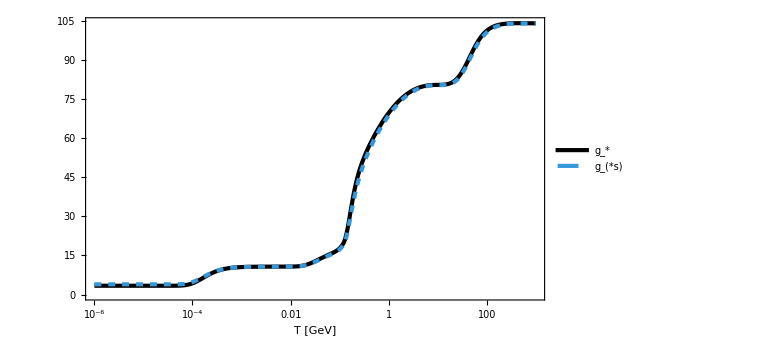

```mathematica
Figgs=LogLinearPlot[{grho[T],gs[T]},{T,10^(-6),10^3},FrameLabel->{Row[{T," [GeV]"}],None},PlotStyle->{{AbsoluteThickness[3],Black},{PETERRIVER,Dashed,AbsoluteThickness[3]}},PlotLegends->Placed[{SubStar[g],Subscript[g, "*s"]},{0.2,0.8}]]//Quiet
```

```mathematica
rho[T_]:=rhohigh[T]/;T>=Tth
rho[T_]:=rholow[T]/;T<Tth
press[T_]:=phigh[T]/;T>=Tth
press[T_]:=plow[T]/;T<Tth
```

```mathematica
EoSw[T_]=press[T]/rho[T];
cs2[T_]:=phigh'[T]/rhohigh'[T]/;T>=Tth
cs2[T_]:=plow'[T]/rholow'[T]/;T<Tth
```

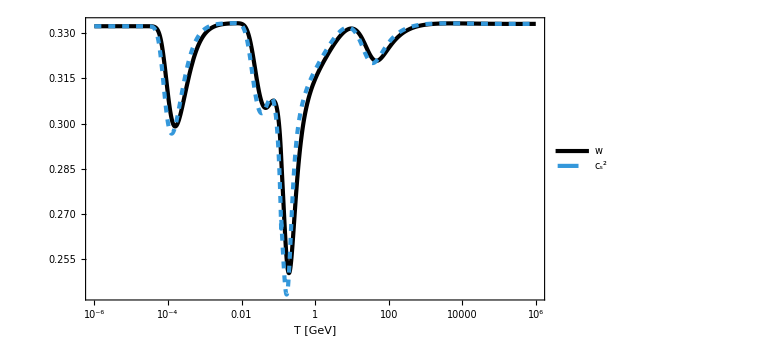

```mathematica
Figwcs=LogLinearPlot[{EoSw[T],cs2[T]},{T,10^-6,10^6},PlotRange->Full,PlotStyle->{{AbsoluteThickness[3],Black},{PETERRIVER,Dashed,AbsoluteThickness[3]}},FrameLabel->{Row[{T," [GeV]"}],None},PlotLegends->Placed[{w,Subscript["c", s]^2},{0.2,0.2}],GridLines->{None,{1/3}}]//Quiet
```

```mathematica
grho0=grho[10^(-6)]//Quiet
gs0=gs[10^(-6)]//Quiet
T0=2.725 KinGeV
```

3.383

3.931

2.34822×10^-13

```mathematica
calH[scalea_,T_]=scalea Sqrt[rho[T]/3/Mpl^2] GeVinMpcinv; (*Mpc^-1*)
calHP[scalea_,T_]=scalea Sqrt[rhoP[T]/3/Mpl^2] GeVinMpcinv; (*Mpc^-1*)
calHM[scalea_,T_]=scalea Sqrt[rhoM[T]/3/Mpl^2] GeVinMpcinv;(*Mpc^-1*)
```

```mathematica
Ti=10^6;
ai=(gs0/gs[Ti])^(1/3) T0/Ti//Quiet
etai=1/calH[ai,Ti]
```

7.86804×10^-20

5.84589×10^-14

```mathematica
etaf=10;
```

```mathematica
bgsol=NDSolve[{T'[eta]==-3(1+EoSw[T[eta]])calH[scalea[eta],T[eta]] grho[T[eta]]/(grhop[T[eta]]+4grho[T[eta]]/T[eta]),scalea'[eta]==scalea[eta]calH[scalea[eta],T[eta]],T[etai]==Ti,scalea[etai]==ai},{T[eta],scalea[eta]},{eta,etai,etaf},WorkingPrecision->30][[1]]//Quiet;//AbsoluteTiming
```

{5.98871,Null}

```mathematica
Tsol[eta_]=T[eta]/. bgsol;
asol[eta_]=scalea[eta]/. bgsol;
```

```mathematica
norm=Tsol[etaf]/T0 asol[etaf]//Quiet
anorm[eta_]=asol[eta/norm]/norm;
Tnorm[eta_]=Tsol[eta/norm];
calHnorm[eta_]=calH[anorm[eta],Tnorm[eta]];
af=anorm[norm etaf]//Quiet;
calHf=calHnorm[norm etaf]//Quiet;
```

0.989259

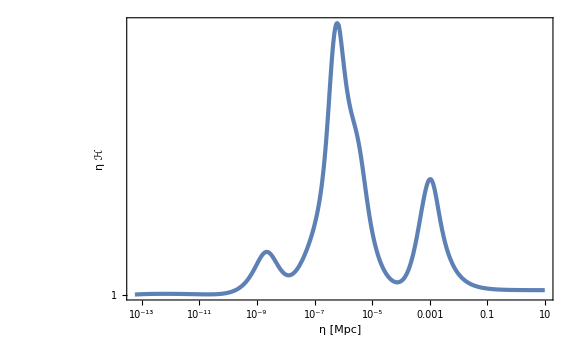

```mathematica
LogLogPlot[{eta calHnorm[eta]},{eta,norm etai,norm etaf},PlotRange->Full,FrameLabel->{"η [Mpc]",η ℋ}]
```

```mathematica
EoSwsol[eta_]=EoSw[Tnorm[eta]];
cs2sol[eta_]:=cs2[Tnorm[eta]];
grhosol[eta_]=grho[Tnorm[eta]];
gssol[eta_]=gs[Tnorm[eta]];
```

```mathematica
anormList=Table[{10^logeta,anorm[10^logeta]//Quiet},{logeta,Log10[norm etai],Log10[norm etaf],10^-2}];
aint[eta_]=Interpolation[anormList][eta];
calHList=Table[{10^logeta,calHnorm[10^logeta]//Quiet},{logeta,Log10[norm etai],Log10[norm etaf],10^-2}];
calHint[eta_]=Interpolation[calHList][eta];
EoSwList=Table[{10^logeta,EoSwsol[10^logeta]//Quiet},{logeta,Log10[norm etai],Log10[norm etaf],10^-2}];
cs2List=Table[{10^logeta,cs2sol[10^logeta]//Quiet},{logeta,Log10[norm etai],Log10[norm etaf],10^-2}];
EoSwint[eta_]=Interpolation[EoSwList][eta];
cs2int[eta_]=Interpolation[cs2List][eta];
grhoList=Table[{10^logeta,grhosol[10^logeta]//Quiet},{logeta,Log10[norm etai],Log10[norm etaf],10^-2}];
gsList=Table[{10^logeta,gssol[10^logeta]//Quiet},{logeta,Log10[norm etai],Log10[norm etaf],10^-2}];
grhoint[eta_]=Interpolation[grhoList][eta];
gsint[eta_]=Interpolation[gsList][eta];
```

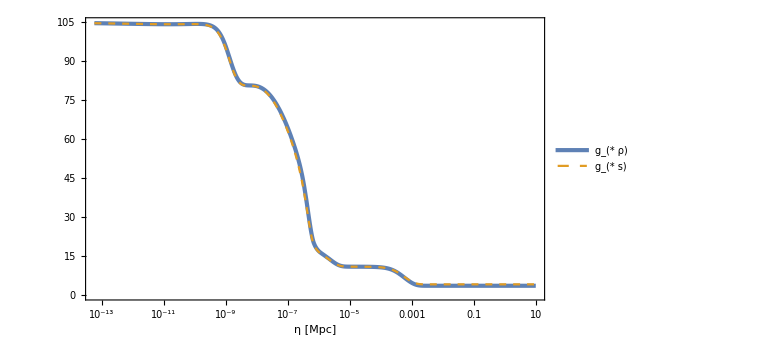

```mathematica
LogLinearPlot[{grhoint[eta],gsint[eta]},{eta,etai,etaf},PlotStyle->{AbsoluteThickness[3],Dashed},PlotLegends->Placed[{Subscript[g,"*"ρ],Subscript[g,"*"s]},{0.8,0.8}],FrameLabel->{"η [Mpc]",None}]
```

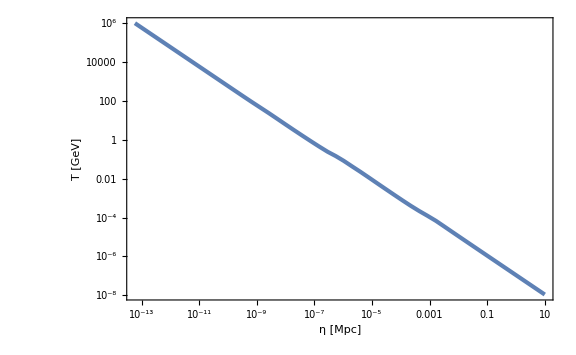

```mathematica
Tvseta=LogLogPlot[{Tsol[eta]},{eta,etai,etaf},FrameLabel->{Row[{η," [Mpc]"}],Row[{T," [GeV]"}]}]
```

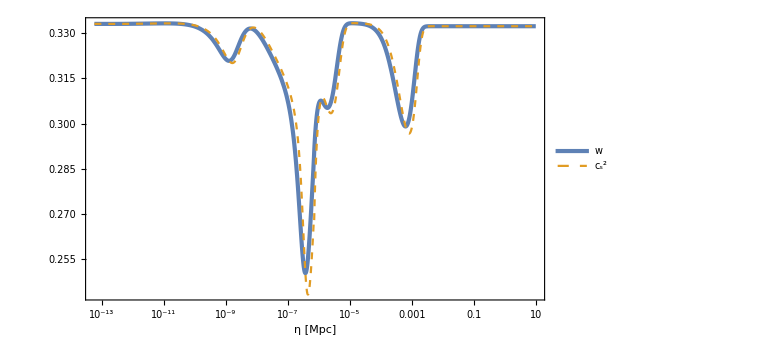

```mathematica
LogLinearPlot[{EoSwint[eta],cs2int[eta]},{eta,etai,etaf},PlotRange->Full,PlotStyle->{AbsoluteThickness[3],Dashed},FrameLabel->{Row[{η," [Mpc]"}],None},PlotLegends->Placed[{w,Subscript["c", s]^2},{0.2,0.2}]]//Quiet
```

### scalar

```mathematica
(*xi=10^-2;*)
xf=1000;
```

```mathematica
kmin=10^5;
dk=kmin;
kmax=10^8;
```

```mathematica
PhiList[eta_]=ParallelTable[{(*k=10^logk;*)k,ptbsol=NDSolve[{Phi''[eta]+3calHint[eta](1+cs2int[eta]) Phi'[eta]+(cs2int[eta]k^2+3calHint[eta]^2(cs2int[eta]-EoSwint[eta]))Phi[eta]==0,Phi[etai]==1,Phi'[etai]==0},Phi[eta],{eta,norm etai,xf/k},(*WorkingPrecision->30,*)MaxSteps->10^5][[1]];
Phi[eta]/. ptbsol},(*{logk,(*4*)5,10,10^-2}*){k,kmin,kmax,dk}];//AbsoluteTiming
Clear[k];
```

{77.6587,Null}

```mathematica
PhipList[eta_]=ParallelTable[{PhiList[eta][[i,1]],D[PhiList[eta][[i,2]],eta]},{i,Length[PhiList[eta]]}];
```

```mathematica
calPList[x_]=ParallelTable[{k=PhiList[x/k][[i,1]];k,PhiList[x/k][[i,2]]^2+PhipList[x/k][[i,2]]^2/k^2/cs2int[x/k]},{i,Length[PhiList[x]]}];//AbsoluteTiming
Clear[k];
```

{230.401,Null}

```mathematica
PhiRad[x_]=9/x^2 (Sin[x/Sqrt[3]]/(x/Sqrt[3])-Cos[x/Sqrt[3]]);
calPRad[x_]=PhiRad[x]^2+PhiRad'[x]^2/(1/3);
NormcalP8=calPList[8].DiagonalMatrix[{1,calPRad[8]^(-1)}];
```

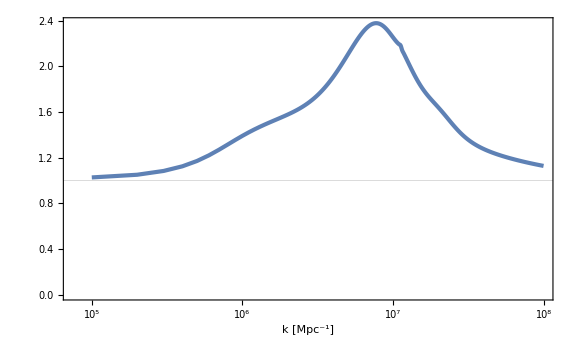

```mathematica
FigScalarAverage=ListLogLinearPlot[{NormcalP8},GridLines->{None,{1}},FrameLabel->{{None,None},{Row[{k," [",Superscript[Mpc,-1],"]"}],k η==8}}]
```

### GW

```mathematica
xi=10^-2;
xf=1000;
```

```mathematica
Clear[k];
G1List[eta_]=ParallelTable[(*k=10^logk;*)
ptbsol=NDSolve[{G''[eta]+(k^2-(1-3EoSwint[eta])/2*calHint[eta]^2)G[eta]==0,G[xi/k]==1,G'[xi/k]==0},G[eta],{eta,xi/k,xf/k},MaxSteps->10^6
(*,WorkingPrecision->10*)(*,AccuracyGoal->10*),PrecisionGoal->10][[1]];
{k,G[eta]/.ptbsol},(*{logk,(*4*)5,10,10^-2}*){k,kmin,kmax,dk}];//AbsoluteTiming
G2List[eta_]=ParallelTable[(*k=10^logk;*)
ptbsol=NDSolve[{G''[eta]+(k^2-(1-3EoSwint[eta])/2*calHint[eta]^2)G[eta]==0,G'[xi/k]==k,G[xi/k]==0},G[eta],{eta,xi/k,xf/k},MaxSteps->10^6
(*,WorkingPrecision->10*)(*,AccuracyGoal->10*),PrecisionGoal->10][[1]];
{k,G[eta]/.ptbsol},(*{logk,(*4*)5,10,10^-2}*){k,kmin,kmax,dk}];//AbsoluteTiming
Clear[k];
```

{62.4322,Null}

{60.9313,Null}

InterpolatingFunction::dmval: Input value {2.77073×10^-10} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

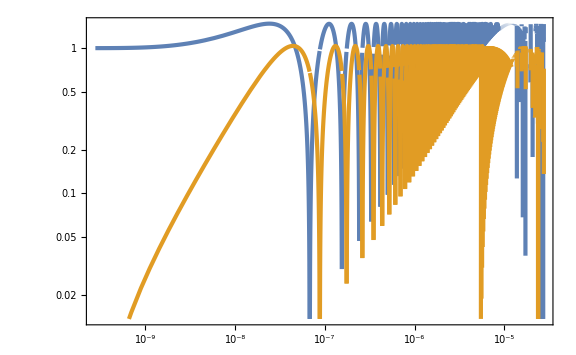

```mathematica
LogLogPlot[{Abs[G1List[eta][[361,2]]],Abs[G2List[eta][[361,2]]]},{eta,xi/G1List[eta][[361,1]],xf/G1List[eta][[361,1]]}]
```

### convolution

```mathematica
kList=Table[PhiList[eta][[i,1]],{i,Length[PhiList[eta]]}];
```

```mathematica
xi=10^-2;
xc=400;
xf=1000;
dx=π;
(*dlogk=10^-2 Log[10];dlogk//N*)
iMax=Length[kList]
```

1000

```mathematica
PhiMode[eta_]=Table[UnitStep[(*eta-xi/kList[[i]],*)xf/kList[[i]]-eta] PhiList[eta][[i,2]],{i,Length[PhiList[eta]]}];
PhipMode[eta_]=Table[UnitStep[(*eta-xi/kList[[i]],*)xf/kList[[i]]-eta] D[PhiMode[eta][[i]],eta],{i,Length[PhiList[eta]]}];
```

```mathematica
G1Mode[eta_]=Table[G1List[eta][[i,2]],{i,Length[G1List[eta]]}];
G1pMode[eta_]=Table[D[G1Mode[eta][[i]],eta],{i,Length[G1Mode[eta]]}];
G2Mode[eta_]=Table[G2List[eta][[i,2]],{i,Length[G2List[eta]]}];
G2pMode[eta_]=Table[D[G2Mode[eta][[i]],eta],{i,Length[G2Mode[eta]]}];
```

```mathematica
ItGen1[i1_,i2_,iGW_,eta_]:=kList[[iGW]] NIntegrate[aint[etap] G1Mode[etap][[iGW]] (2PhiMode[etap][[i1]] PhiMode[etap][[i2]]+4/3/(1+EoSwint[etap]) (PhiMode[etap][[i1]]+PhipMode[etap][[i1]]/calHint[etap]) (PhiMode[etap][[i2]]+PhipMode[etap][[i2]]/calHint[etap])),{etap,xi/kList[[iGW]],eta}
(*,Method->{"GlobalAdaptive","SymbolicProcessing"->0}*)
(*,PrecisionGoal->10*)
(*,WorkingPrecision->50,MaxRecursion->20*)]
ItGen2[i1_,i2_,iGW_,eta_]:=kList[[iGW]] NIntegrate[aint[etap] G2Mode[etap][[iGW]] (2PhiMode[etap][[i1]] PhiMode[etap][[i2]]+4/3/(1+EoSwint[etap]) (PhiMode[etap][[i1]]+PhipMode[etap][[i1]]/calHint[etap]) (PhiMode[etap][[i2]]+PhipMode[etap][[i2]]/calHint[etap])),{etap,xi/kList[[iGW]],eta}
(*,Method->{"GlobalAdaptive","SymbolicProcessing"->0}*)
(*,PrecisionGoal->10*)
(*,WorkingPrecision->50,MaxRecursion->20*)]
ItGen2bar[i_,eta_,ItG1_,ItG2_]:=ItG1^2 (G2Mode[(kList[[i]]eta-dx/2)/kList[[i]]][[i]]^2+G2Mode[(kList[[i]]eta-dx/4)/kList[[i]]][[i]]^2+G2Mode[(kList[[i]]eta)/kList[[i]]][[i]]^2+G2Mode[(kList[[i]]eta+dx/4)/kList[[i]]][[i]]^2)/4+ItG2^2 (G1Mode[(kList[[i]]eta-dx/2)/kList[[i]]][[i]]^2+G1Mode[(kList[[i]]eta-dx/4)/kList[[i]]][[i]]^2+G1Mode[(kList[[i]]eta)/kList[[i]]][[i]]^2+G1Mode[(kList[[i]]eta+dx/4)/kList[[i]]][[i]]^2)/4-2 ItG1 ItG2 (G1Mode[(kList[[i]]eta-dx/2)/kList[[i]]][[i]]G2Mode[(kList[[i]]eta-dx/2)/kList[[i]]][[i]]+G1Mode[(kList[[i]]eta-dx/4)/kList[[i]]][[i]]G2Mode[(kList[[i]]eta-dx/4)/kList[[i]]][[i]]+G1Mode[(kList[[i]]eta)/kList[[i]]][[i]]G2Mode[(kList[[i]]eta)/kList[[i]]][[i]]+G1Mode[(kList[[i]]eta+dx/4)/kList[[i]]][[i]]G2Mode[(kList[[i]]eta+dx/4)/kList[[i]]][[i]])/4
```

```mathematica
ItG1=ItGen1[401,401,401,xc/kList[[401]]];//Quiet//AbsoluteTiming
ItG1
ItG2=ItGen2[401,401,401,xc/kList[[401]]];//Quiet//AbsoluteTiming
ItG2
ItGen2bar[401,xc/kList[[401]],ItG1,ItG2]//Quiet//AbsoluteTiming
```

{0.23977,Null}

5.60068×10^-13

{0.168087,Null}

4.88406×10^-13

{0.045528,1.13879×10^-25}

```mathematica
kyr=1/yrins(2π)/MpcinvinHz
```

2.04934×10^7

```mathematica
iNANOmin=Length[Select[kList MpcinvinHz/(2π),#<2 10^-9&]]
iNANOmax=Length[kList]-Length[Select[kList MpcinvinHz/(2π),#>59 10^-9&]]+1
```

12

382

```mathematica
Table[kList[[i]],{i,iNANOmin,iNANOmax,iNANOmin}]//Length
```

31

```mathematica
kList[[iNANOmin]] MpcinvinHz/(2π)
kList[[iNANOmax]] MpcinvinHz/(2π)
```

1.85554×10^-9

5.90681×10^-8

```mathematica
(*i1step=(*2*)1;
i2step=(*5*)1;*)
(*Di=1000;*)
(*Dup=200;
Ddown=100;
Dlogk1=dlogk i1step;Dlogk1//N
Dlogk2=dlogk i2step;Dlogk2//N*)
(*2Di/istep+1*)
istep[k_]=Floor[k/(10dk)];
Dk[k_]=dk istep[k];
kk=kList[[200]]
istep[kk]
Dk[kk]
Select[Flatten[Table[If[Abs[kList[[i1]]-kList[[i2]]]<=kk<=kList[[i1]]+kList[[i2]],{i1,i2},{0}],{i1,(*Max[300-(*Di*)Ddown,1]*)1,(*Min[300+(*Di*)Dup,iMax]*) iMax,(*i1step*)istep[kk]},{i2,(*Max[300-(*Di*)Ddown,1]*)1,(*Min[300+Di,iMax]*)(*iMax*)i1,(*i2step*)istep[kk]}],1],#[[1]]!=0&]//Length
```

20000000

20

2000000

465

```mathematica
ItG1List=ParallelTable[If[Abs[kList[[i1]]-kList[[i2]]]<=kList[[i]]<=kList[[i1]]+kList[[i2]]&&iNANOmin<=i<=iNANOmax&&Mod[i-iNANOmin,5iNANOmin]==0&&Mod[i1-1,istep[kList[[i]]]]==0&&Mod[i2-1,istep[kList[[i]]]]==0,
ItGen1[i1,i2,i,xc/kList[[i]]]//Quiet,
None],{i,iMax},{i1,iMax},{i2,i1}];//AbsoluteTiming
```

$Aborted

```mathematica
ItG2List=ParallelTable[If[Abs[kList[[i1]]-kList[[i2]]]<=kList[[i]]<=kList[[i1]]+kList[[i2]]&&iNANOmin<=i<=iNANOmax&&Mod[i-iNANOmin,5iNANOmin]==0&&Mod[i1-1,istep[kList[[i]]]]==0&&Mod[i2-1,istep[kList[[i]]]]==0,
ItGen2[i1,i2,i,xc/kList[[i]]]//Quiet,
None],{i,iMax},{i1,iMax},{i2,i1}];//AbsoluteTiming
```

```mathematica
OGWc[i_,eta_,ns_]:=2 8/243 (*Dlogk1 Dlogk2*)Dk[kList[[i]]]^2/(aint[eta]calHint[eta])^2*Sum[If[Abs[kList[[i1]]-kList[[i2]]]<=kList[[i]]<=kList[[i1]]+kList[[i2]],((kList[[i1]]kList[[i2]])/kyr^2)^ns 1/(kList[[i1]]kList[[i2]])(kList[[i1]]^2-(kList[[i]]^2-kList[[i2]]^2+kList[[i1]]^2)^2/4/kList[[i]]^2)^2/kList[[i1]]/kList[[i2]]*ItGen2bar[i,eta,ItGen1[i1,i2,i,eta],ItGen2[i1,i2,i,eta]],0],{i1,(*Max[i-(*Di*)Ddown,1]*)1,(*Min[i+(*Di*)Dup,iMax]*) iMax,istep[kList[[i]]]},{i2,(*Max[i-(*Di*)Ddown,1]*)1,(*Min[i+Di,iMax]*)(*iMax*)i1,istep[kList[[i]]]}]
```

```mathematica
OGW0h2[i_,ns_]:=(aint[xc/kList[[i]]]calHint[xc/kList[[i]]]/af/calHf)^2 Or0h2 OGWc[i,xc/kList[[i]],ns];
```

```mathematica
OGW0h2[200,2]//Quiet//AbsoluteTiming
```

$Aborted

```mathematica
OGW0h2List=ParallelTable[{kList[[i]],OGW0h2[i,1]//Quiet},{i,(*1,iMax*)iNANOmin,iNANOmax,(*20*)5}];//AbsoluteTiming
```

$Aborted

```mathematica
(*OGW0h2ListTrim=Select[OGW0h2List.DiagonalMatrix[{MpcinvinHz/(2π),1}],2 10^-9<#[[1]]<59 10^-9&];*)
```

```mathematica
fit[f_]=A(f yrins)^n/. FindFit[OGW0h2List(*Trim*),A(f yrins)^n,{A,n},f]
```

(1.45122×10^-7)/f^0.266732

8.27628×10^7 f^1.70612

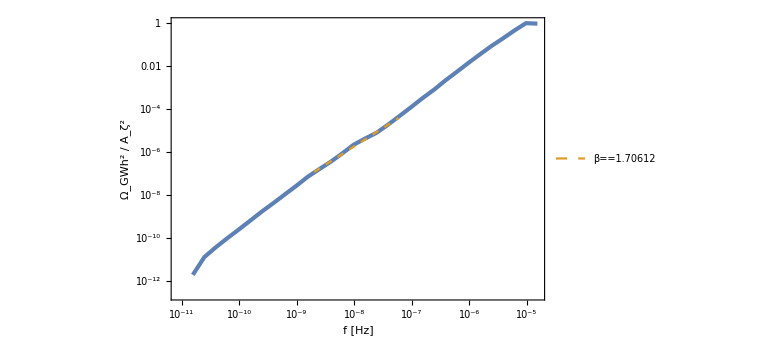

```mathematica
Show[ListLogLogPlot[OGW0h2List.DiagonalMatrix[{MpcinvinHz/(2π),1}],GridLines->{{2 10^-9,59 10^-9},None},FrameLabel->{"f [Hz]","Ω_GWh^2 / A_ζ^2"}],LogLogPlot[fit[f],{f,2 10^-9,59 10^-9},PlotStyle->{Color[2],Dashed},PlotLegends->Placed[{β==n/.FindFit[OGW0h2ListTrim,A(f yrins)^n,{A,n},f]},{0.3,0.2}]]]
```

```mathematica
Log10[2 10^-9]//N
Log10[59 10^-9]//N
```

-8.69897

-7.22915

### NANOGrav

```mathematica
Agamma1sData=Import["Agamma1s.csv"];
Agamma2sData=Import["Agamma2s.csv"];
Agamma3sData=Import["Agamma3s.csv"];
```

```mathematica
Ag1sMean=Mean[Agamma1sData];
Ag2sMean=Mean[Agamma2sData];
Ag3sMean=Mean[Agamma3sData];
```

```mathematica
Ag1sSph=Map[{ArcTan[#[[1]]-Ag1sMean[[1]],#[[2]]-Ag1sMean[[2]]],#[[1]],#[[2]]}&,Agamma1sData];
Ag2sSph=Map[{ArcTan[#[[1]]-Ag2sMean[[1]],#[[2]]-Ag2sMean[[2]]],#[[1]],#[[2]]}&,Agamma2sData];
Ag3sSph=Map[{ArcTan[#[[1]]-Ag3sMean[[1]],#[[2]]-Ag3sMean[[2]]],#[[1]],#[[2]]}&,Agamma3sData];
```

```mathematica
Agamma1sSort=Map[{#[[1]],10^(#[[2]])}&,Sort[Ag1sSph][[All,2;;3]]];
Agamma2sSort=Map[{#[[1]],10^(#[[2]])}&,Sort[Ag2sSph][[All,2;;3]]];
Agamma3sSort=Map[{#[[1]],10^(#[[2]])}&,Sort[Ag3sSph][[All,2;;3]]];
```

```mathematica
Agamma1s=Join[Agamma1sSort,{Agamma1sSort[[1]]}];
Agamma2s=Join[Agamma2sSort,{Agamma2sSort[[1]]}];Agamma3s=Join[Agamma3sSort,{Agamma3sSort[[1]]}];
```

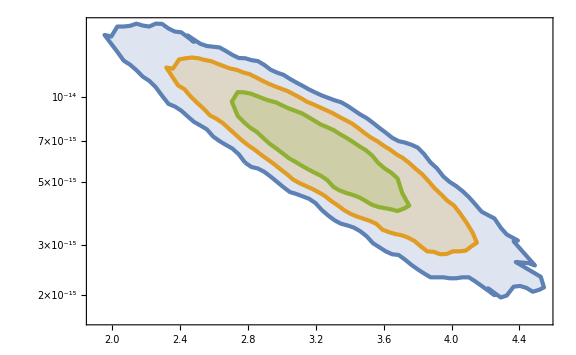

```mathematica
ListLogPlot[{Agamma3s,Agamma2s,Agamma1s},Filling->Bottom]
```

```mathematica
Ωyrh2[A_]=(2π)/3(1/(100 10^3/Mpcinm))^2 A^2 yrins^-2;
β[γ_]=5-γ;
```

```mathematica
Ωbeta1s=Map[{β[#[[1]]],Ωyrh2[#[[2]]]}&,Agamma1s];
Ωbeta2s=Map[{β[#[[1]]],Ωyrh2[#[[2]]]}&,Agamma2s];
Ωbeta3s=Map[{β[#[[1]]],Ωyrh2[#[[2]]]}&,Agamma3s];
```

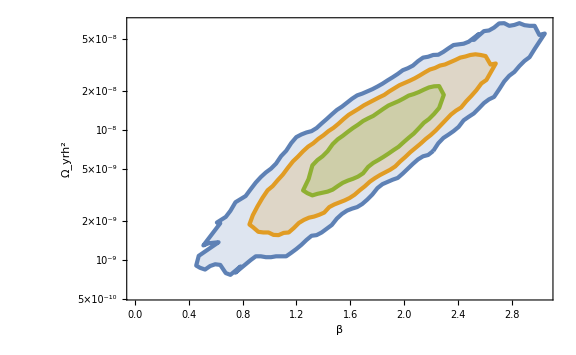

```mathematica
ListLogPlot[{Ωbeta3s,Ωbeta2s,Ωbeta1s},Filling->Bottom,FrameLabel->{β,"Ω_yrh^2"}]
```

```mathematica
QnsKTList=Transpose[{{0.4,0.6,0.8,1.0,1.2,1.4,1.6,1.8,2.0,2.2,2.4},{0.8196,0.7984,0.7956,0.8222,0.8988,1.074,1.470,2.478,5.783,24.77,708.2}}];
```

```mathematica
QnsKTint[ns_]=Interpolation[QnsKTList,InterpolationOrder->1][ns];
```

```mathematica
I2RDmean[u_,v_]=1/2((3(u^2+v^2-3))/(4 u^3 v^3))^2((-4u v+(u^2+v^2-3)Log[Abs[(3-(u+v)^2)/(3-(u-v)^2)]])^2+π^2(u^2+v^2-3)^2 UnitStep[v+u-Sqrt[3]]);
```

```mathematica
uu[t_,s_]=(t+s+1)/2;
vv[t_,s_]=(t-s+1)/2;
```

```mathematica
1/yrins//N
```

3.16888×10^-8

```mathematica
kyr=1/yrins(2π)/MpcinvinHz;kyr//N
```

2.04935×10^7

### quadratic

```mathematica
kmin=10^5;
kmax1=10^8;
kNANOmin=2π (2 10^-9)/MpcinvinHz;kNANOmin//N
kNANOmax=2π (59 10^-9)/MpcinvinHz;kNANOmax//N
```

1.29342×10^6

3.81559×10^7

```mathematica
Log10[1/yrins]//N
```

-7.49909

```mathematica
kmax1/kNANOmin 10//N
```

773.143

```mathematica
Clear[OGWh2RD1]
OGWh2RD1[k_,ns_]:=Or0h2 1/24 2NIntegrate[((t(2+t)(s^2-1))/((1-s+t)(1+s+t)))^2 I2RDmean[uu[t,s],vv[t,s]]((uu[t,s]k)/kyr)^(ns-1)UnitStep[(*uu[t,s]k-kmin,*)kmax1-uu[t,s]k]((vv[t,s]k)/kyr)^(ns-1)UnitStep[(*vv[t,s]k-kmin,*)kmax1-vv[t,s]k],{t,0,kmax1/k 10},{s,-1,1},WorkingPrecision->30,MinRecursion->4]
```

```mathematica
OGWh2RDmin=OGWh2RD1[kNANOmin,10]
OGWh2RDmax=OGWh2RD1[10^7,10]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.8959921008813823705184981823914122612957300671503788264630766567768837137646306×10^8 and 2811.5620942678047685903224678185990380886395910944922466523798283734923166490327 for the integral and error estimates.

663.597235308483829681474363837

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.9976911917139966094793275895495153794051881914618362823210879875929434775470839×10^10 and 1.4734726902782505962271749724947564011636876060940727657626252052068014412328028×10^6 for the integral and error estimates.

69919.1917099898813317764656342

```mathematica
Log[OGWh2RD1max/OGWh2RD1min]/Log[kNANOmax/kNANOmin]
```

2.68704234461222854880632903376

```mathematica
OGWh2RD1List=ParallelTable[{ns-1,Table[{10^lnk,OGWh2RD1[10^lnk,ns]//Quiet},{lnk,Log10[kNANOmin],Log10[kNANOmax],10^-1}]},{ns,1,6,10^-1}];//AbsoluteTiming
```

{1177.82,Null}

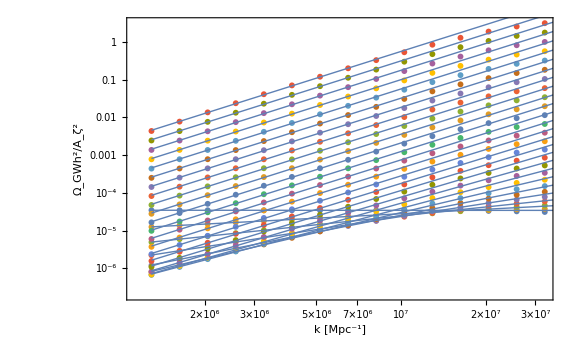

```mathematica
Show[ListLogLogPlot[Table[OGWh2RD1List[[i,2]],{i,1,Length[OGWh2RD1List],2}],Joined->False,GridLines->{{kyr},None},FrameLabel->{{"Ω_GWh^2/A_ζ^2",None},{"k [Mpc^-1]","k_max = 10^8 Mpc^-1"}}],LogLogPlot[Table[Exp[lnQRD] (k/kyr)^βRD/.FindFit[Log[Select[OGWh2RD1List[[i,2]],#[[1]]<10^7&]],lnQRD+βRD(lnk-Log[kyr]),{lnQRD,βRD},lnk],{i,1,Length[OGWh2RD1List],2}],{k,kNANOmin,kNANOmax},PlotStyle->{Thin}]]
```

```mathematica
QnsRD1List=Table[{OGWh2RD1List[[i,1]],Exp[lnQRD]/.FindFit[Log[Select[OGWh2RD1List[[i,2]],#[[1]]<10^7&]],lnQRD+βRD(lnk-Log[kyr]),{lnQRD,βRD},lnk]},{i,Length[OGWh2RD1List]}];
βnsRD1List=Table[{OGWh2RD1List[[i,1]],βRD/.FindFit[Log[Select[OGWh2RD1List[[i,2]],#[[1]]<10^7&]],lnQRD+βRD(lnk-Log[kyr]),{lnQRD,βRD},lnk]},{i,Length[OGWh2RD1List]}];
```

```mathematica
QnsRD1fit[nsm1_]=10^(aa+bb Tanh[cc (nsm1-dd)])/.FindFit[Map[{#[[1]],Log10[#[[2]]]}&,QnsRD1List],aa+bb Tanh[cc (x-dd)],{aa,bb,cc,dd},x](*10^(aa nsm1^2+bb nsm1+cc)/.FindFit[Map[{#[[1]],Log10[#[[2]]]}&,QnsRD1List],aa x^2+bb x+cc,{aa,bb,cc},x]*)
```

10^(-1.03377814466436758723072155112+4.66788086782208726577304474335 Tanh[0.263632907143305980656402503143 (-3.7612777104678188464416070991+nsm1)])

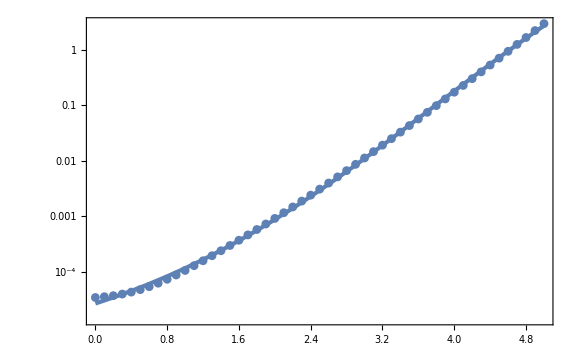

```mathematica
Show[ListLogPlot[QnsRD1List,Joined->False],LogPlot[QnsRD1fit[nsm1],{nsm1,0,5}]]
```

```mathematica
βnsRD1fit[nsm1_]=aa nsm1^2+bb nsm1+cc/.FindFit[βnsRD1List,aa nsm1^2+bb nsm1+cc,{aa,bb,cc},nsm1]
```

0.427540679445808600764209006636+1.25882560096187747483620124355 nsm1-0.187186482669008038656487675679 nsm1^2

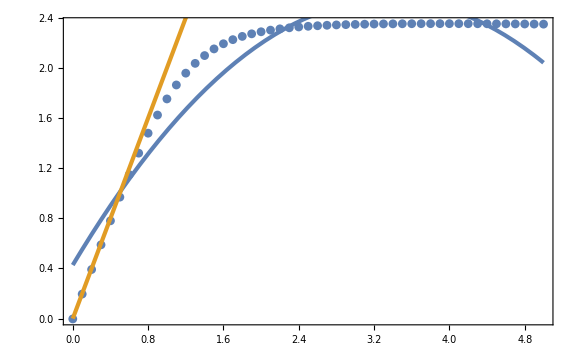

```mathematica
Show[ListPlot[βnsRD1List,Joined->False],Plot[{βnsRD1fit[nsm1],2nsm1},{nsm1,0,5}]]
```

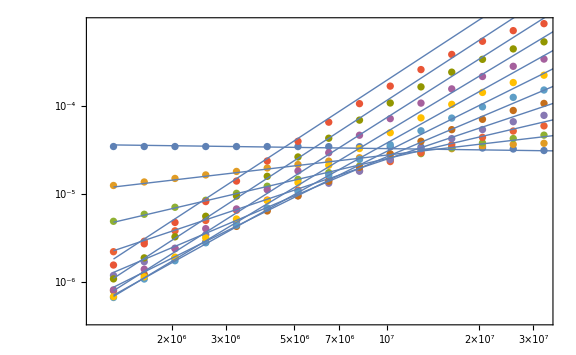

```mathematica
Show[ListLogLogPlot[Table[OGWh2RD1List[[i,2]],{i,1,Length[OGWh2RD1List],2}],Joined->False,GridLines->{{kyr},None}],LogLogPlot[Table[QnsRD1fit[OGWh2RD1List[[i,1]]] (k/kyr)^βnsRD1fit[OGWh2RD1List[[i,1]]],{i,1,Length[OGWh2RD1List],2}],{k,kNANOmin,kNANOmax},PlotStyle->{Thin}]]
```

```mathematica
QnsQCD[nsm1_]=10^(1.101 nsm1^2+0.1618nsm1-4.931);
```

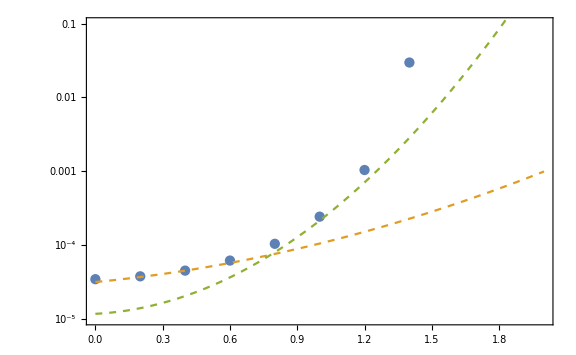

```mathematica
Show[ListLogPlot[Map[{#[[1]]-1,Or0h2#[[2]]}&,QnsKTList],PlotRange->{{0,2},{10^-5,0.1}},Joined->False],LogPlot[{QnsRD1fit[nsm1],QnsQCD[nsm1]},{nsm1,0,2},PlotStyle->{{Color[2],Dashed},{Color[3],Dashed}}]]
```

```mathematica
kmax2=5 10^7;
```

```mathematica
Clear[OGWh2RD2]
OGWh2RD2[k_,ns_]:=Or0h2 1/24 2NIntegrate[((t(2+t)(s^2-1))/((1-s+t)(1+s+t)))^2 I2RDmean[uu[t,s],vv[t,s]]((uu[t,s]k)/kyr)^(ns-1)UnitStep[uu[t,s]k-kmin,kmax2-uu[t,s]k]((vv[t,s]k)/kyr)^(ns-1)UnitStep[vv[t,s]k-kmin,kmax2-vv[t,s]k],{t,0,10^3},{s,-1,1},WorkingPrecision->30,MinRecursion->4]
```

```mathematica
OGWh2RD2[kNANOmin,2]
OGWh2RD2[kNANOmax,2]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in t near {t,s} = {0.73206713696681518250276353194270831973190679447334532316617395654218246887278178,-0.019484549899269668892398204106648529679569040211521924964907652982191706314531714}. NIntegrate obtained 0.20474347287344727511101161365646847030114778601240191519496244691873701267923041 and 9.834833158811921817892705647918869216770465922263654412137417451869543657303717×10^-6 for the integral and error estimates.

7.16602155057065462888540647798×10^-7

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in t near {t,s} = {0.73206713696681518250276353194270831973190679447334532316617395654218246887278178,0.10551545010073033110760179589335147032043095978847807503509234701780829368546829}. NIntegrate obtained 3.9858178831470628306576290234627821456704367950682824401050454344327042628697836 and 0.00080592953787689813485297959895229659762430258244080684160425551967947776359106903 for the integral and error estimates.

0.0000139503625910147199073017015821

```mathematica
OGWh2RD2List=ParallelTable[{ns-1,Table[{10^lnk,OGWh2RD2[10^lnk,ns]//Quiet},{lnk,Log10[kNANOmin],Log10[kNANOmax],10^-1}]},{ns,1,3,10^-1}];//AbsoluteTiming
```

{336.411,Null}

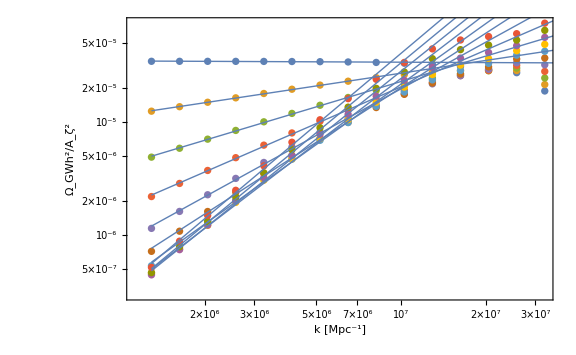

```mathematica
Show[ListLogLogPlot[Table[OGWh2RD2List[[i,2]],{i,1,Length[OGWh2RD2List],2}],Joined->False,GridLines->{{kyr},None},FrameLabel->{{"Ω_GWh^2/A_ζ^2",None},{"k [Mpc^-1]","k_max = 5 × 10^7 Mpc^-1"}}],LogLogPlot[Table[Exp[lnQRD] (k/kyr)^βRD/.FindFit[Log[Select[OGWh2RD2List[[i,2]],#[[1]]<10^7&]],lnQRD+βRD(lnk-Log[kyr]),{lnQRD,βRD},lnk],{i,1,Length[OGWh2RD2List],2}],{k,kNANOmin,kNANOmax},PlotStyle->{Thin}]]
```

```mathematica
QnsRD2List=Table[{OGWh2RD2List[[i,1]],Exp[lnQRD]/.FindFit[Log[Select[OGWh2RD2List[[i,2]],#[[1]]<10^7&]],lnQRD+βRD(lnk-Log[kyr]),{lnQRD,βRD},lnk]},{i,Length[OGWh2RD2List]}];
βnsRD2List=Table[{OGWh2RD2List[[i,1]],βRD/.FindFit[Log[Select[OGWh2RD2List[[i,2]],#[[1]]<10^7&]],lnQRD+βRD(lnk-Log[kyr]),{lnQRD,βRD},lnk]},{i,Length[OGWh2RD2List]}];
```

```mathematica
QnsRD2fit[nsm1_]=10^(aa nsm1^2+bb nsm1+cc)/.FindFit[Map[{#[[1]],Log10[#[[2]]]}&,QnsRD2List],aa x^2+bb x+cc,{aa,bb,cc},x]
```

10^(-4.493460054932857998168626496164+0.2020098569944929373626809843226 nsm1+0.09120848759941361423043135101875 nsm1^2)

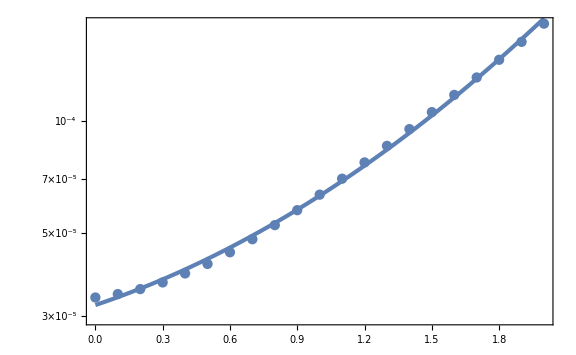

```mathematica
Show[ListLogPlot[QnsRD2List,Joined->False],LogPlot[QnsRD2fit[nsm1],{nsm1,0,2}]]
```

```mathematica
βnsRD2fit[nsm1_]=aa nsm1^2+bb nsm1+cc/.FindFit[βnsRD2List,aa nsm1^2+bb nsm1+cc,{aa,bb,cc},nsm1]
```

-0.0250722275793854014067612512795+2.173863151345019834107042310781 nsm1-0.5640397458816630085150409085312 nsm1^2

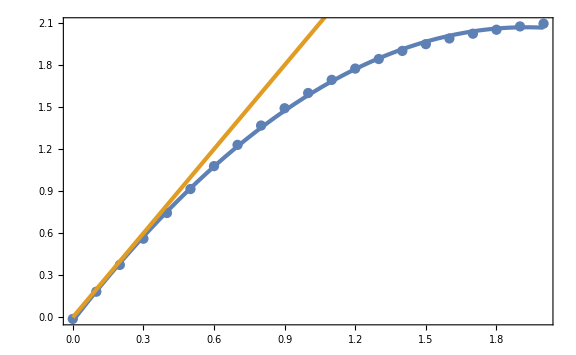

```mathematica
Show[ListPlot[βnsRD2List,Joined->False],Plot[{βnsRD2fit[nsm1],2nsm1},{nsm1,0,2}]]
```

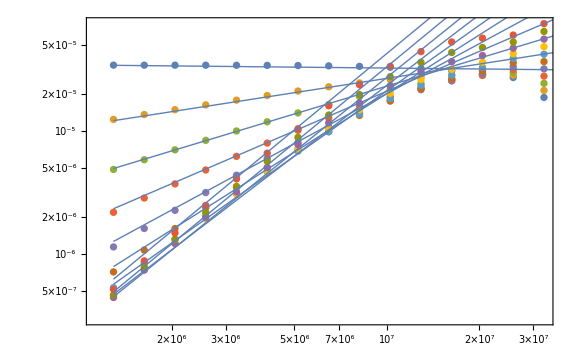

```mathematica
Show[ListLogLogPlot[Table[OGWh2RD2List[[i,2]],{i,1,Length[OGWh2RD2List],2}],Joined->False,GridLines->{{kyr},None}],LogLogPlot[Table[QnsRD2fit[OGWh2RD2List[[i,1]]] (k/kyr)^βnsRD2fit[OGWh2RD2List[[i,1]]],{i,1,Length[OGWh2RD2List],2}],{k,kNANOmin,kNANOmax},PlotStyle->{Thin}]]
```

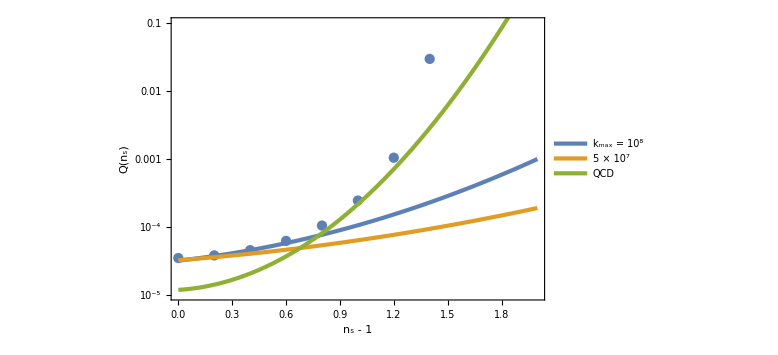

```mathematica
Show[ListLogPlot[Map[{#[[1]]-1,Or0h2#[[2]]}&,QnsKTList],PlotRange->{{0,2},{10^-5,0.1}},Joined->False,FrameLabel->{"n_(<s>) - 1",Q[Subscript[n, s]]}],LogPlot[{QnsRD1fit[nsm1],QnsRD2fit[nsm1],QnsQCD[nsm1]},{nsm1,0,2},PlotRange->Full,PlotLegends->Placed[{"k_max = 10^8","5 × 10^7","QCD"},{0.2,0.7}]]]
```

```mathematica
Export["QnsRD.dat",OGWh2RDList];
```

```mathematica
10^-4.2(10^7)^1.4
```

398107.

```mathematica
nsm1RD1[beta_]=(-bb+Sqrt[bb^2-4aa(cc-beta)])/(2aa)/.FindFit[βnsRD1List,aa nsm1^2+bb nsm1+cc,{aa,bb,cc},nsm1]//Simplify
nsm1RD2[beta_]=(-bb+Sqrt[bb^2-4aa(cc-beta)])/(2aa)/.FindFit[βnsRD2List,aa nsm1^2+bb nsm1+cc,{aa,bb,cc},nsm1]//Simplify
```

1.94495455567851780527840175015-0.812637129587057856348203411914 √(5.61252551416821303870628034996-2.46112308579390341521640656857 beta)

1.92704784300883463138565132828-0.8864623524330522761628342984964 √(4.66911406928544554992187533548-2.256158983526652034060163634125 beta)

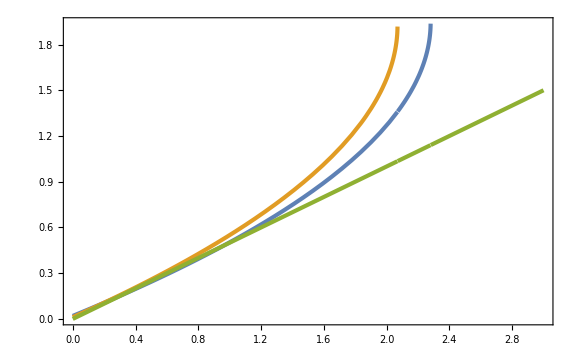

```mathematica
Plot[{nsm1RD1[beta],nsm1RD2[beta],beta/2},{beta,0,3}]
```

```mathematica
InverseFunction[(aa #^2+bb #+cc)&][beta]
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

(-bb-√(bb^2+4 aa beta-4 aa cc))/(2 aa)

```mathematica
AzRD1[Oh2_,nsm1_]=Sqrt[Oh2/QnsRD1fit[nsm1]];
AzRD2[Oh2_,nsm1_]=Sqrt[Oh2/QnsRD2fit[nsm1]];
AzQCD[Oh2_,nsm1_]=Sqrt[Oh2/QnsQCD[nsm1]];
nsm1QCD[beta_]=(beta+0.2404)/2.133;
```

```mathematica
AnsRD11s=Map[{nsm1RD1[#[[1]]],AzRD1[#[[2]],nsm1RD1[#[[1]]]]}&,Ωbeta1s];
AnsRD12s=Map[{nsm1RD1[#[[1]]],AzRD1[#[[2]],nsm1RD1[#[[1]]]]}&,Ωbeta2s];
AnsRD13s=Map[{nsm1RD1[#[[1]]],AzRD1[#[[2]],nsm1RD1[#[[1]]]]}&,Ωbeta3s];
AnsRD21s=Map[{nsm1RD2[#[[1]]],AzRD2[#[[2]],nsm1RD2[#[[1]]]]}&,Ωbeta1s];
AnsRD22s=Map[{nsm1RD2[#[[1]]],AzRD2[#[[2]],nsm1RD2[#[[1]]]]}&,Ωbeta2s];
AnsRD23s=Map[{nsm1RD2[#[[1]]],AzRD2[#[[2]],nsm1RD2[#[[1]]]]}&,Ωbeta3s];
AnsQCD1s=Map[{nsm1QCD[#[[1]]],AzQCD[#[[2]],nsm1QCD[#[[1]]]]}&,Ωbeta1s];
AnsQCD2s=Map[{nsm1QCD[#[[1]]],AzQCD[#[[2]],nsm1QCD[#[[1]]]]}&,Ωbeta2s];
AnsQCD3s=Map[{nsm1QCD[#[[1]]],AzQCD[#[[2]],nsm1QCD[#[[1]]]]}&,Ωbeta3s];
```

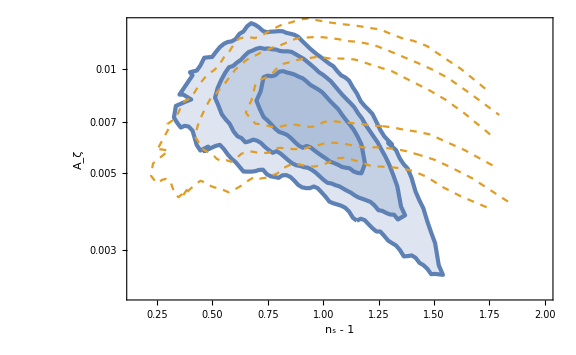

```mathematica
Show[ListLogPlot[{AnsQCD3s,AnsQCD2s,AnsQCD1s},PlotRange->{{0.15,2},Automatic}(*{{1.2,2.6},{5 10^-4,0.03}}*),Filling->Bottom,FrameLabel->{"n_(<s>) - 1",Subscript[A, ζ]},PlotStyle->{{AbsoluteThickness[3],Color[1]}}],ListLogPlot[{AnsRD13s,AnsRD12s,AnsRD11s},PlotStyle->{{Dashed,Color[2]}},PlotRange->Full]]
```

```mathematica
W[z_]=E^(-z^2/2);
```

```mathematica
16/81 Az Integrate[W[k R]^2(k R)^4(k/ks)^(ns-1)1/k,{k,0,∞},Assumptions->{ns>0,R>0}]//Simplify
```

8/81 Az ks (1/(ks R))^ns R Gamma[(3+ns)/2]

```mathematica
δrms[R_]=Sqrt[16/81 Az Integrate[W[k R]^2(k R)^4(k/ks)^(ns-1)1/k,{k,0,∞},Assumptions->{ns>0,R>0}]]//Simplify
```

2/9 √2 √(Az ks (1/(ks R))^ns R Gamma[(3+ns)/2])

```mathematica
Msol=1.989 10^33;
```

```mathematica
1/(1.56 10^13)
```

6.41026×10^-14

```mathematica
Rsol=R/.Solve[10^20(50/106.75)^(-1/6)(R 1.56 10^13)^2==Msol,R][[2]]
```

2.68376×10^-7

```mathematica
RinM[M_]=Rsol(M/Ms)^(1/2)
```

2.68376×10^-7 √(M/Ms)

```mathematica
δrms[RinM[Ms]]
```

0.000162807 √((3.72612×10^6)^ns Az (1/ks)^(-1+ns) Gamma[(3+ns)/2])

```mathematica
δrms[RinM[Ms]]/.{ns->2,Az->0.007,ks->kyr}
```

0.0129268

### broken line

```mathematica
kmin=10^5;
kmax1=10^8;
kNANOmin=2π (2 10^-9)/MpcinvinHz;kNANOmin//N
kNANOmax=2π (59 10^-9)/MpcinvinHz;kNANOmax//N
```

1.29342×10^6

3.81559×10^7

```mathematica
kmax1/kNANOmin//N
```

77.3143

```mathematica
Log10[1/yrins]//N
```

-7.49909

```mathematica
Clear[OGWh2RD1]
OGWh2RD1[k_,ns_]:=Or0h2 1/24 2NIntegrate[((t(2+t)(s^2-1))/((1-s+t)(1+s+t)))^2 I2RDmean[uu[t,s],vv[t,s]]((uu[t,s]k)/kyr)^(ns-1)UnitStep[(*uu[t,s]k-kmin,*)kmax1-uu[t,s]k]((vv[t,s]k)/kyr)^(ns-1)UnitStep[(*vv[t,s]k-kmin,*)kmax1-vv[t,s]k],{t,0,10 kmax1/k},{s,-1,1},WorkingPrecision->30,MinRecursion->4]
```

```mathematica
OGWh2RD1min=OGWh2RD1[kNANOmin,4]
OGWh2RD1max=OGWh2RD1[kNANOmax,4]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.7073911466392658982287103003322003390348295724999820271101340759859476881520046 and 0.000016121062172113654650093571736201142346483099287291997422426566403715457399768643 for the integral and error estimates.

0.0000164758690132374306438004860512

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3347.2933490050737412531003659483625417468909554099133561011175317749356237571543 and 0.57968908172056925785546101501100649276956487826350562088379126441582051028881502 for the integral and error estimates.

0.0117155267215177580943858512808

```mathematica
Log[OGWh2RD1max/OGWh2RD1min]/Log[kNANOmax/kNANOmin]
```

1.94031213124431010552305517265

```mathematica
OGWh2RD1List=ParallelTable[{ns-1,Table[{10^lnk,OGWh2RD1[10^lnk,ns]//Quiet},{lnk,Log10[kNANOmin],Log10[kNANOmax],10^-1}]},{ns,0,5,10^-1}];//AbsoluteTiming
```

{968.962,Null}

```mathematica
Export["OGWh2RD1.mat",OGWh2RD1List];
```

```mathematica
Export["OGWh2RD1e+8.dat",OGWh2RD1List[[All,2,All,2]]];
```

```mathematica
Export["nsList.dat",OGWh2RD1List[[All,1]]];
```

```mathematica
Export["kList.dat",OGWh2RD1List[[All,2,All,1]][[1]]];
```

```mathematica
Export["OGWh2RD1e+8ns3.dat",OGWh2RD1List[[21,2]]];
```

```mathematica
OGWh2RD1List=Map[{#[[1,1,1]],#[[2]]}&,Import["OGWh2RD1.mat"][[1]]];
```

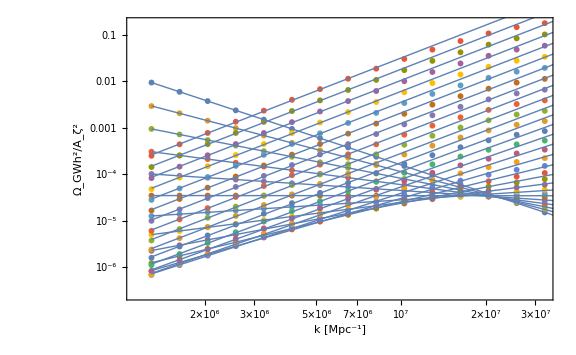

```mathematica
Show[ListLogLogPlot[Table[OGWh2RD1List[[i,2]],{i,1,Length[OGWh2RD1List],2}],Joined->False,GridLines->{{kyr},None},FrameLabel->{{"Ω_GWh^2/A_ζ^2",None},{"k [Mpc^-1]","k_max = 10^8 Mpc^-1"}}],LogLogPlot[Table[Exp[lnQRD] (k/kyr)^βRD/.FindFit[Log[Select[OGWh2RD1List[[i,2]],#[[1]]<10^7&]],lnQRD+βRD(lnk-Log[kyr]),{lnQRD,βRD},lnk],{i,1,Length[OGWh2RD1List],2}],{k,kNANOmin,kNANOmax},PlotStyle->{Thin}]]
```

```mathematica
QnsRD1List=Table[{OGWh2RD1List[[i,1]],Exp[lnQRD]/.FindFit[Log[Select[OGWh2RD1List[[i,2]],#[[1]]<10^7&]],lnQRD+βRD(lnk-Log[kyr]),{lnQRD,βRD},lnk]},{i,Length[OGWh2RD1List]}];
βnsRD1List=Table[{OGWh2RD1List[[i,1]],βRD/.FindFit[Log[Select[OGWh2RD1List[[i,2]],#[[1]]<10^7&]],lnQRD+βRD(lnk-Log[kyr]),{lnQRD,βRD},lnk]},{i,Length[OGWh2RD1List]}];
```

```mathematica
aQRD1=aa/.FindFit[Map[{#[[1]],Log10[#[[2]]]}&,Select[QnsRD1List,#[[1]]<-0.6&]],aa x+bb,{aa,bb},x]
bQRD1=bb/.FindFit[Map[{#[[1]],Log10[#[[2]]]}&,Select[QnsRD1List,#[[1]]<-0.6&]],aa x+bb,{aa,bb},x]
cQRD1=cc/.FindFit[Map[{#[[1]],Log10[#[[2]]]}&,Select[QnsRD1List,#[[1]]>2&]],cc x+dd,{cc,dd},x]
dQRD1=dd/.FindFit[Map[{#[[1]],Log10[#[[2]]]}&,Select[QnsRD1List,#[[1]]>2&]],cc x+dd,{cc,dd},x]
FindFit[Map[{#[[1]],Log10[#[[2]]]}&,QnsRD1List],aQRD1 x+bQRD1+ee Log10[1+10^((cQRD1 x+dQRD1-(aQRD1 x+bQRD1))/ee)],ee,x]
QnsRD1fit[nsm1_]=10^(aQRD1 nsm1+bQRD1)(1+10^((cQRD1 nsm1+dQRD1-(aQRD1 nsm1+bQRD1))/ee))^ee/.FindFit[Map[{#[[1]],Log10[#[[2]]]}&,QnsRD1List],aQRD1 x+bQRD1+ee Log10[1+10^((cQRD1 x+dQRD1-(aQRD1 x+bQRD1))/ee)],ee,x]
```

-0.100814

-4.52341

1.14771

-5.37533

{ee→1.25303}

10^(-4.52341-0.100814 nsm1) (1+10^(0.798065 (-0.851922+1.24853 nsm1)))^1.25303

```mathematica
bQRD1p=Log10[Select[QnsRD1List,#[[1]]>=0&][[1,2]]]
QRD1fitp=FindFit[Map[{#[[1]],Log10[#[[2]]]}&,Select[QnsRD1List,#[[1]]>=0&]],bb+ee Log10[1+10^((cQRD1 x+dQRD1-bb)/ee)],{{bb,bQRD1p},ee},x]
QnsRD1fitp[nsm1_]=10^bb(1+10^((cQRD1 nsm1+dQRD1-bb)/ee))^ee/.QRD1fitp
```

-4.46439

{bb→-4.65391,ee→1.39963}

0.0000221864 (1+10^(0.714474 (-0.721417+1.14771 nsm1)))^1.39963

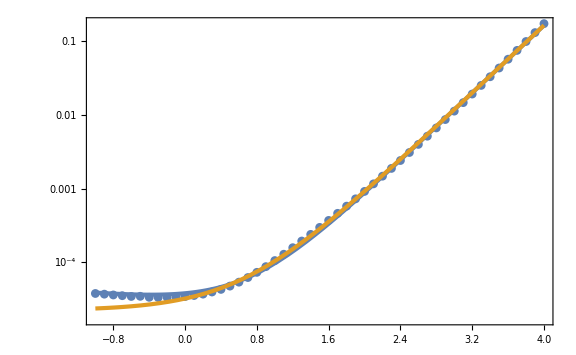

```mathematica
Show[ListLogPlot[QnsRD1List,Joined->False],LogPlot[{QnsRD1fit[nsm1],QnsRD1fitp[nsm1]},{nsm1,-1,4}]]
```

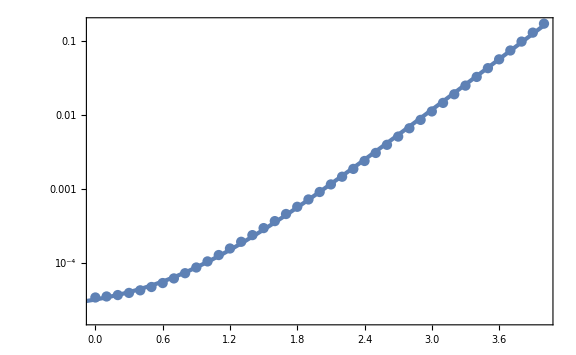

```mathematica
Show[ListLogPlot[Select[QnsRD1List,#[[1]]>=0&],Joined->False],LogPlot[QnsRD1fitp[nsm1],{nsm1,-1,4}]]
```

```mathematica
aβRD1=aa/.FindFit[Select[βnsRD1List,#[[1]]<1&],aa x+bb,{aa,bb},x]
bβRD1=bb/.FindFit[Select[βnsRD1List,#[[1]]<1&],aa x+bb,{aa,bb},x]
cβRD1=cc/.FindFit[Select[βnsRD1List,#[[1]]>2&],cc x+dd,{cc,dd},x]
dβRD1=dd/.FindFit[Select[βnsRD1List,#[[1]]>2&],cc x+dd,{cc,dd},x]
FindFit[βnsRD1List,aβRD1 x+bβRD1+ee Log10[1+10^((cβRD1 x+dβRD1-(aβRD1 x+bβRD1))/ee)],ee,x]
βnsRD1fit[nsm1_]=aβRD1 nsm1+bβRD1+ee Log10[1+10^((cβRD1 nsm1+dβRD1-(aβRD1 nsm1+bβRD1))/ee)]/.FindFit[βnsRD1List,aβRD1 x+bβRD1+ee Log10[1+10^((cβRD1 x+dβRD1-(aβRD1 x+bβRD1))/ee)],ee,x]
```

1.93864

-0.0270267

0.0227431

2.2725

{ee→-1.08018}

-0.0270267+1.93864 nsm1-0.469117 Log[1+10^(-0.92577 (2.29953-1.91589 nsm1))]

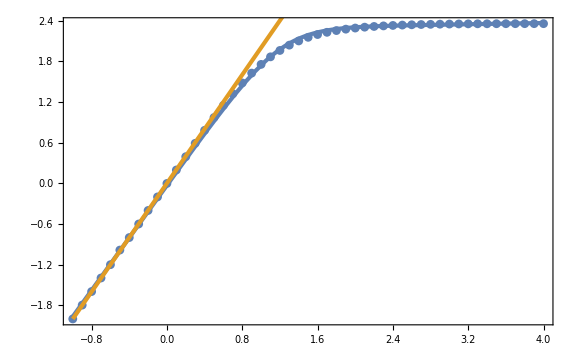

```mathematica
Show[ListPlot[βnsRD1List,Joined->False],Plot[{βnsRD1fit[nsm1],2nsm1},{nsm1,-1,4}]]
```

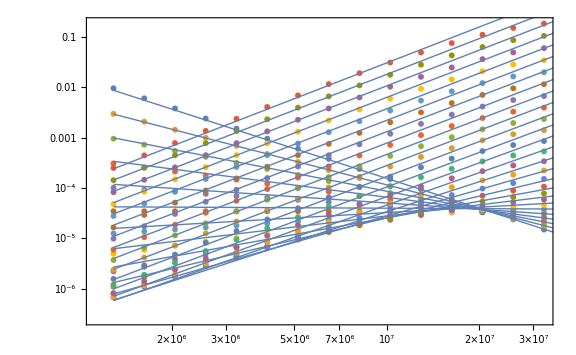

```mathematica
Show[ListLogLogPlot[Table[OGWh2RD1List[[i,2]],{i,1,Length[OGWh2RD1List],2}],Joined->False,GridLines->{{kyr},None}],LogLogPlot[Table[QnsRD1fit[OGWh2RD1List[[i,1]]] (k/kyr)^βnsRD1fit[OGWh2RD1List[[i,1]]],{i,1,Length[OGWh2RD1List],2}],{k,kNANOmin,kNANOmax},PlotStyle->{Thin}]]
```

```mathematica
Export["QRD1e+8.dat",QnsRD1List];
Export["betaRD1e+8.dat",βnsRD1List];
```

```mathematica
QnsQCD[nsm1_]=10^(1.101 nsm1^2+0.1618nsm1-4.931);
```

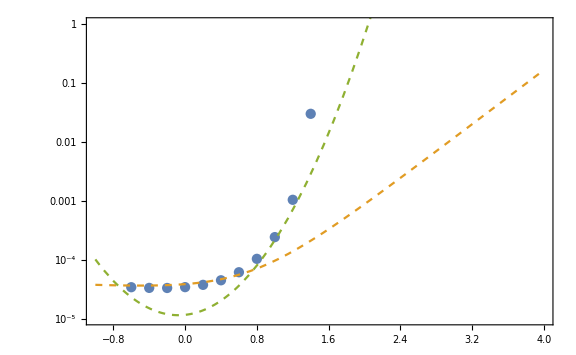

```mathematica
Show[ListLogPlot[Map[{#[[1]]-1,Or0h2#[[2]]}&,QnsKTList],PlotRange->{{-1,4},{10^-5,1}},Joined->False],LogPlot[{QnsRD1fit[nsm1],QnsQCD[nsm1]},{nsm1,-1,4},PlotStyle->{{Color[2],Dashed},{Color[3],Dashed}}]]
```

```mathematica
kmax2=5 10^7;
```

```mathematica
Clear[OGWh2RD2]
OGWh2RD2[k_,ns_]:=Or0h2 1/24 2NIntegrate[((t(2+t)(s^2-1))/((1-s+t)(1+s+t)))^2 I2RDmean[uu[t,s],vv[t,s]]((uu[t,s]k)/kyr)^(ns-1)UnitStep[(*uu[t,s]k-kmin,*)kmax2-uu[t,s]k]((vv[t,s]k)/kyr)^(ns-1)UnitStep[(*vv[t,s]k-kmin,*)kmax2-vv[t,s]k],{t,0,10 kmax2/k},{s,-1,1},WorkingPrecision->30,MinRecursion->4]
```

```mathematica
OGWh2RD2min=OGWh2RD2[kNANOmin,4]
OGWh2RD2max=OGWh2RD2[kNANOmax,4]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.40015175142763657942116254892804619280212023192153075546998511907556385242392829 and 2.6168684039501291517373626932470012368505346810861305064403507803519440760920656×10^-6 for the integral and error estimates.

1.40053112999672802797406892125×10^-6

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in t near {t,s} = {0.73205258602813405973160634361531200316742996659578701147717083424004056409751479,-0.019484549899269668892398204106648529679569040211521924964907652982191706314531714}. NIntegrate obtained 131.73664542639374873200821712095876620940672452049196459771694847915729737775497 and 0.056723391719658396539452504430657726656091372689049918797123880260482410328813891 for the integral and error estimates.

0.000461078258992378120562028759923

```mathematica
Log[OGWh2RD2max/OGWh2RD2min]/Log[kNANOmax/kNANOmin]
```

1.7127800854788876862631523404

```mathematica
OGWh2RD2List=ParallelTable[{ns-1,Table[{10^lnk,OGWh2RD2[10^lnk,ns]//Quiet},{lnk,Log10[kNANOmin],Log10[kNANOmax],10^-1}]},{ns,0,5,10^-1}];//AbsoluteTiming
```

{957.686,Null}

```mathematica
Export["OGWh2RD2.mat",OGWh2RD2List];
```

```mathematica
Export["OGWh2RD5e+7.dat",OGWh2RD2List[[All,2,All,2]]];
```

```mathematica
Export["OGWh2RD5e+7ns3.dat",OGWh2RD2List[[21,2]]];
```

```mathematica
OGWh2RD2List=Map[{#[[1,1,1]],#[[2]]}&,Import["OGWh2RD2.mat"][[1]]];
```

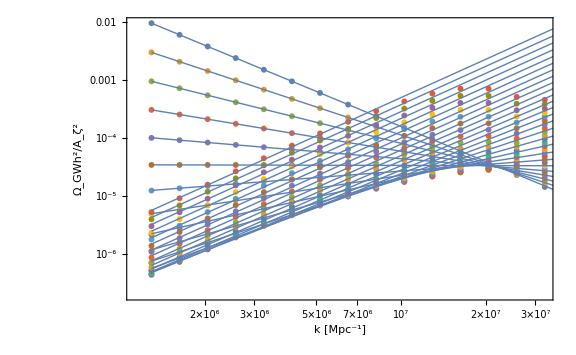

```mathematica
Show[ListLogLogPlot[Table[OGWh2RD2List[[i,2]],{i,1,Length[OGWh2RD2List],2}],Joined->False,GridLines->{{kyr},None},FrameLabel->{{"Ω_GWh^2/A_ζ^2",None},{"k [Mpc^-1]","k_max = 5 × 10^7 Mpc^-1"}}],LogLogPlot[Table[Exp[lnQRD] (k/kyr)^βRD/.FindFit[Log[Select[OGWh2RD2List[[i,2]],#[[1]]<10^7&]],lnQRD+βRD(lnk-Log[kyr]),{lnQRD,βRD},lnk],{i,1,Length[OGWh2RD2List],2}],{k,kNANOmin,kNANOmax},PlotStyle->{Thin}]]
```

```mathematica
QnsRD2List=Table[{OGWh2RD2List[[i,1]],Exp[lnQRD]/.FindFit[Log[Select[OGWh2RD2List[[i,2]],#[[1]]<10^7&]],lnQRD+βRD(lnk-Log[kyr]),{lnQRD,βRD},lnk]},{i,Length[OGWh2RD2List]}];
βnsRD2List=Table[{OGWh2RD2List[[i,1]],βRD/.FindFit[Log[Select[OGWh2RD2List[[i,2]],#[[1]]<10^7&]],lnQRD+βRD(lnk-Log[kyr]),{lnQRD,βRD},lnk]},{i,Length[OGWh2RD2List]}];
```

```mathematica
aQRD2=aa/.FindFit[Map[{#[[1]],Log10[#[[2]]]}&,Select[QnsRD2List,#[[1]]<0&]],aa x+bb,{aa,bb},x]
bQRD2=bb/.FindFit[Map[{#[[1]],Log10[#[[2]]]}&,Select[QnsRD2List,#[[1]]<0&]],aa x+bb,{aa,bb},x]
cQRD2=cc/.FindFit[Map[{#[[1]],Log10[#[[2]]]}&,Select[QnsRD2List,#[[1]]>2&]],cc x+dd,{cc,dd},x]
dQRD2=dd/.FindFit[Map[{#[[1]],Log10[#[[2]]]}&,Select[QnsRD2List,#[[1]]>2&]],cc x+dd,{cc,dd},x]
FindFit[Map[{#[[1]],Log10[#[[2]]]}&,QnsRD2List],aQRD2 x+bQRD2+ee Log10[1+10^((cQRD2 x+dQRD2-(aQRD2 x+bQRD2))/ee)],ee,x]
QnsRD2fit[nsm1_]=10^(aQRD2 nsm1+bQRD2)(1+10^((cQRD2 nsm1+dQRD2-(aQRD2 nsm1+bQRD2))/ee))^ee/.FindFit[Map[{#[[1]],Log10[#[[2]]]}&,QnsRD2List],aQRD2 x+bQRD2+ee Log10[1+10^((cQRD2 x+dQRD2-(aQRD2 x+bQRD2))/ee)],ee,x]
```

-0.0644972

-4.49642

0.562559

-4.88919

{ee→0.637835}

10^(-4.49642-0.0644972 nsm1) (1+10^(1.5678 (-0.392764+0.627056 nsm1)))^0.637835

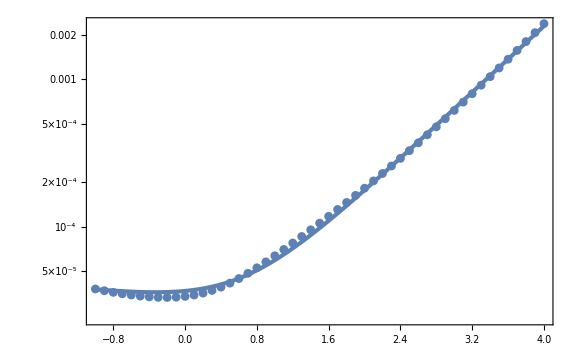

```mathematica
Show[ListLogPlot[QnsRD2List,Joined->False],LogPlot[QnsRD2fit[nsm1],{nsm1,-1,4}]]
```

```mathematica
aβRD2=aa/.FindFit[Select[βnsRD2List,#[[1]]<1&],aa x+bb,{aa,bb},x]
bβRD2=bb/.FindFit[Select[βnsRD2List,#[[1]]<1&],aa x+bb,{aa,bb},x]
cβRD2=cc/.FindFit[Select[βnsRD2List,#[[1]]>2&],cc x+dd,{cc,dd},x]
dβRD2=dd/.FindFit[Select[βnsRD2List,#[[1]]>2&],cc x+dd,{cc,dd},x]
FindFit[βnsRD2List,aβRD2 x+bβRD2+ee Log10[1+10^((cβRD2 x+dβRD2-(aβRD2 x+bβRD2))/ee)],ee,x]
βnsRD2fit[nsm1_]=aβRD2 nsm1+bβRD2+ee Log10[1+10^((cβRD2 nsm1+dβRD2-(aβRD2 nsm1+bβRD2))/ee)]/.FindFit[βnsRD2List,aβRD2 x+bβRD2+ee Log10[1+10^((cβRD2 x+dβRD2-(aβRD2 x+bβRD2))/ee)],ee,x]
```

1.88181

-0.0600743

0.0330747

2.06686

{ee→-1.14369}

-0.0600743+1.88181 nsm1-0.4967 Log[1+10^(-0.87436 (2.12693-1.84874 nsm1))]

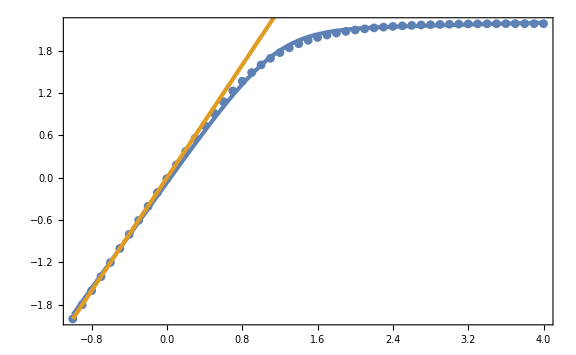

```mathematica
Show[ListPlot[βnsRD2List,Joined->False],Plot[{βnsRD2fit[nsm1],2nsm1},{nsm1,-1,4}]]
```

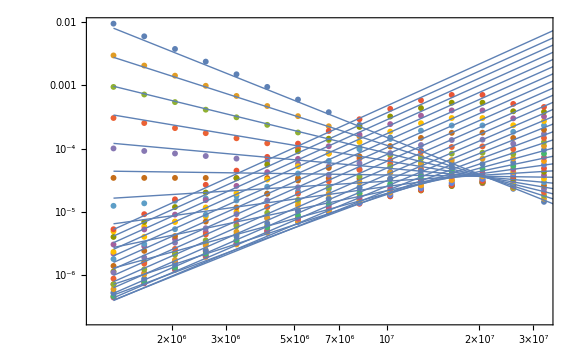

```mathematica
Show[ListLogLogPlot[Table[OGWh2RD2List[[i,2]],{i,1,Length[OGWh2RD2List],2}],Joined->False,GridLines->{{kyr},None}],LogLogPlot[Table[QnsRD2fit[OGWh2RD2List[[i,1]]] (k/kyr)^βnsRD2fit[OGWh2RD2List[[i,1]]],{i,1,Length[OGWh2RD2List],2}],{k,kNANOmin,kNANOmax},PlotStyle->{Thin}]]
```

```mathematica
Export["QRD5e+7.dat",QnsRD2List];
Export["betaRD5e+7.dat",βnsRD2List];
```

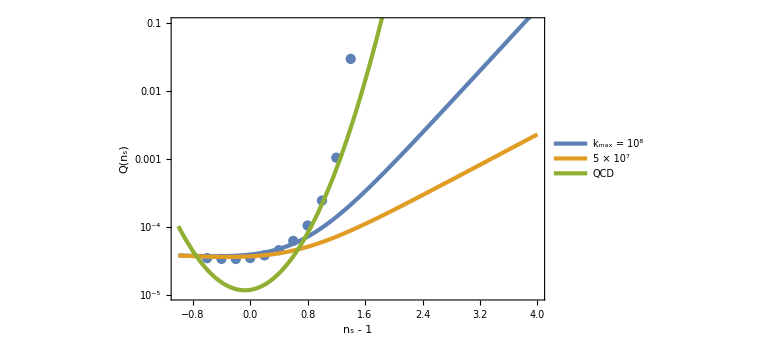

```mathematica
Show[ListLogPlot[Map[{#[[1]]-1,Or0h2#[[2]]}&,QnsKTList],PlotRange->{{-1,4},{10^-5,0.1}},Joined->False,FrameLabel->{"n_(<s>) - 1",Q[Subscript[n, s]]}],LogPlot[{QnsRD1fit[nsm1],QnsRD2fit[nsm1],QnsQCD[nsm1]},{nsm1,-1,4},PlotRange->Full,PlotLegends->Placed[{"k_max = 10^8","5 × 10^7","QCD"},{0.2,0.7}]]]
```

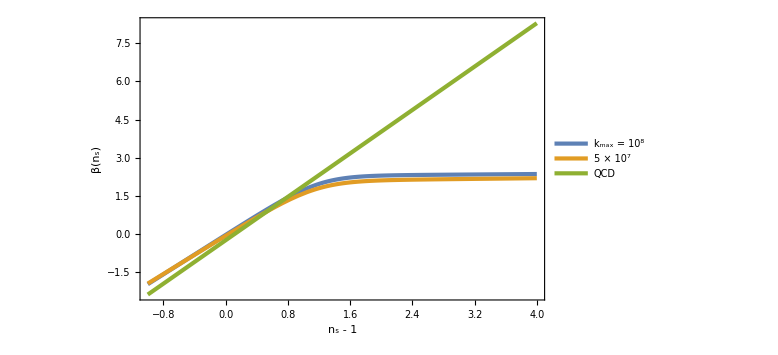

```mathematica
Plot[{βnsRD1fit[nsm1],βnsRD2fit[nsm1],2.133nsm1-0.2404},{nsm1,-1,4},PlotLegends->Placed[{"k_max = 10^8","5 × 10^7","QCD"},{0.2,0.7}],FrameLabel->{"n_(<s>) - 1","β"[Subscript[n, "s"]]}]
```

```mathematica
nsm1RD1[beta_]=(beta-bβRD1)/aβRD1+ee Log10[1+10^(((beta-dβRD1)/cβRD1-(beta-bβRD1)/aβRD1)/ee)]/.FindFit[Map[{#[[2]],#[[1]]}&,βnsRD1List],(x-bβRD1)/aβRD1+ee Log10[1+10^(((x-dβRD1)/cβRD1-(x-bβRD1)/aβRD1)/ee)],ee,x]
nsm1RD2[beta_]=(beta-bβRD2)/aβRD2+ee Log10[1+10^(((beta-dβRD2)/cβRD2-(beta-bβRD2)/aβRD2)/ee)]/.FindFit[Map[{#[[2]],#[[1]]}&,βnsRD2List],(x-bβRD2)/aβRD2+ee Log10[1+10^(((x-dβRD2)/cβRD2-(x-bβRD2)/aβRD2)/ee)],ee,x]
```

0.51582669932389562501739429089 (0.0270266545670908438809728624676+beta)+0.850374581494211585987827604526 Log[1+10^(0.510709622975963829874792969828 (43.9694559953893809816186081665 (-2.27249940309466103515495943327+beta)-0.51582669932389562501739429089 (0.0270266545670908438809728624676+beta)))]

0.531402248320663739833987135909 (0.0600743250220171851846430460189+beta)+0.913172572848916411881956008543 Log[1+10^(0.475588617985250705207549313132 (30.2346003597583687671185401049 (-2.06685665042000112547877446537+beta)-0.531402248320663739833987135909 (0.0600743250220171851846430460189+beta)))]

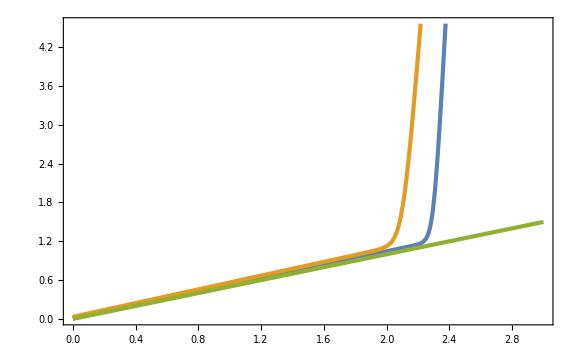

```mathematica
Plot[{nsm1RD1[beta],nsm1RD2[beta],beta/2},{beta,0,3}]
```

```mathematica
AzRD1[Oh2_,nsm1_]=Sqrt[Oh2/QnsRD1fit[nsm1]];
AzRD2[Oh2_,nsm1_]=Sqrt[Oh2/QnsRD2fit[nsm1]];
AzQCD[Oh2_,nsm1_]=Sqrt[Oh2/QnsQCD[nsm1]];
nsm1QCD[beta_]=(beta+0.2404)/2.133;
```

```mathematica
AnsRD11s=Map[{nsm1RD1[#[[1]]],AzRD1[#[[2]],nsm1RD1[#[[1]]]]}&,Ωbeta1s];
AnsRD12s=Map[{nsm1RD1[#[[1]]],AzRD1[#[[2]],nsm1RD1[#[[1]]]]}&,Ωbeta2s];
AnsRD13s=Map[{nsm1RD1[#[[1]]],AzRD1[#[[2]],nsm1RD1[#[[1]]]]}&,Ωbeta3s];
AnsRD21s=Map[{nsm1RD2[#[[1]]],AzRD2[#[[2]],nsm1RD2[#[[1]]]]}&,Ωbeta1s];
AnsRD22s=Map[{nsm1RD2[#[[1]]],AzRD2[#[[2]],nsm1RD2[#[[1]]]]}&,Ωbeta2s];
AnsRD23s=Map[{nsm1RD2[#[[1]]],AzRD2[#[[2]],nsm1RD2[#[[1]]]]}&,Ωbeta3s];
AnsQCD1s=Map[{nsm1QCD[#[[1]]],AzQCD[#[[2]],nsm1QCD[#[[1]]]]}&,Ωbeta1s];
AnsQCD2s=Map[{nsm1QCD[#[[1]]],AzQCD[#[[2]],nsm1QCD[#[[1]]]]}&,Ωbeta2s];
AnsQCD3s=Map[{nsm1QCD[#[[1]]],AzQCD[#[[2]],nsm1QCD[#[[1]]]]}&,Ωbeta3s];
```

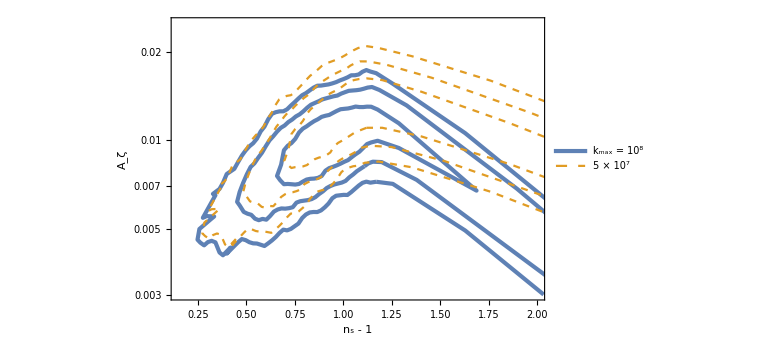

```mathematica
ListLogPlot[{AnsRD13s,AnsRD12s,AnsRD11s,AnsRD23s,AnsRD22s,AnsRD21s},PlotRange->{{0.15,2},{0.003,0.025}},PlotStyle->{{Color[1],AbsoluteThickness[3]},{Color[1],AbsoluteThickness[3]},{Color[1],AbsoluteThickness[3]},{Color[2],Dashed},{Color[2],Dashed},{Color[2],Dashed}},FrameLabel->{"n_(<s>) - 1",Subscript[A, ζ]},PlotLegends->Placed[LineLegend[{"k_max = 10^8",None,None,"5 × 10^7"},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.15,0.85}]]
```

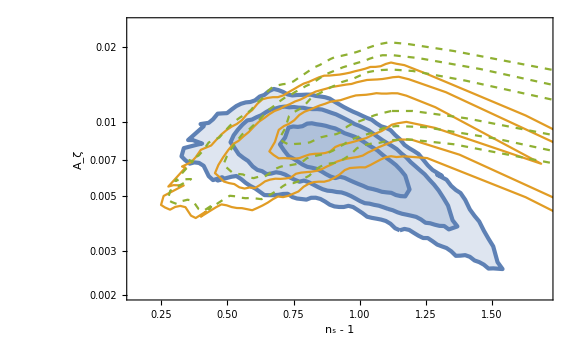

```mathematica
Show[ListLogPlot[{AnsQCD3s,AnsQCD2s,AnsQCD1s},PlotRange->{{0.15,1.7},{0.002,0.025}}(*{{1.2,2.6},{5 10^-4,0.03}}*),Filling->Bottom,FrameLabel->{"n_(<s>) - 1",Subscript[A, ζ]},PlotStyle->{{AbsoluteThickness[3],Color[1]}}],ListLogPlot[{AnsRD13s,AnsRD12s,AnsRD11s,AnsRD23s,AnsRD22s,AnsRD21s},PlotStyle->{{Color[2]},{Color[2]},{Color[2]},{Dashed,Color[3]},{Dashed,Color[3]},{Dashed,Color[3]}},PlotRange->Full]]
```

```mathematica
W[z_]=E^(-z^2/2);
```

```mathematica
16/81 Az Integrate[W[k R]^2(k R)^4(k/ks)^(ns-1)1/k,{k,0,∞},Assumptions->{ns>0,R>0}]//Simplify
```

8/81 Az ks (1/(ks R))^ns R Gamma[(3+ns)/2]

```mathematica
δrms[R_]=Sqrt[16/81 Az Integrate[W[k R]^2(k R)^4(k/ks)^(ns-1)1/k,{k,0,∞},Assumptions->{ns>0,R>0}]]//Simplify
```

2/9 √2 √(Az ks (1/(ks R))^ns R Gamma[(3+ns)/2])

```mathematica
Msol=1.989 10^33;
```

```mathematica
1/(1.56 10^13)
```

6.41026×10^-14

```mathematica
Rsol=R/.Solve[10^20(50/106.75)^(-1/6)(R 1.56 10^13)^2==Msol,R][[2]]
```

2.68376×10^-7

```mathematica
RinM[M_]=Rsol(M/Ms)^(1/2)
```

2.68376×10^-7 √(M/Ms)

```mathematica
δrms[RinM[Ms]]
```

0.000162807 √((3.72612×10^6)^ns Az (1/ks)^(-1+ns) Gamma[(3+ns)/2])

```mathematica
δrms[RinM[Ms]]/.{ns->2,Az->0.007,ks->kyr}
```

0.0129268

### abe

```mathematica
QnsQCD1fit[nsm1_]=10^aa(1+10^((bb nsm1+cc-aa)/dd))^dd/.{aa->−4.854,bb->1.139,cc->−5.593,dd->1.068};
QnsRD1fit[nsm1_]=10^aa(1+10^((bb nsm1+cc-aa)/dd))^dd/.{aa->-4.684,bb->1.155,cc->−5.328,dd->1.420};
QnsQCD2fit[nsm1_]=10^aa(1+10^((bb nsm1+cc-aa)/dd))^dd/.{aa->−4.829,bb->0.5616,cc->−5.170,dd->0.6002};
QnsRD2fit[nsm1_]=10^aa(1+10^((bb nsm1+cc-aa)/dd))^dd/.{aa->−4.702,bb->0.5718,cc->−4.899,dd->0.9659};
```

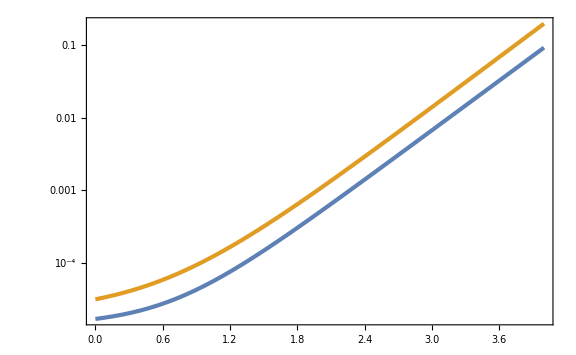

```mathematica
LogPlot[{QnsQCD1fit[nsm1],QnsRD1fit[nsm1]},{nsm1,0,4}]
```

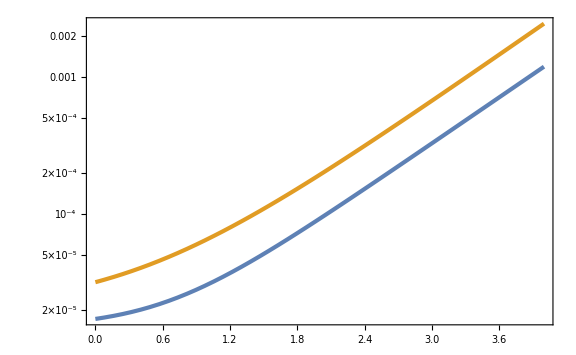

```mathematica
LogPlot[{QnsQCD2fit[nsm1],QnsRD2fit[nsm1]},{nsm1,0,4}]
```

```mathematica
βnsQCD1fit[nsm1_]=ee Tanh[ff nsm1]-gg/.{ee->2.636,ff->0.8752,gg->0.1983};
βnsRD1fit[nsm1_]=ee Tanh[ff nsm1]-gg/.{ee->2.431,ff->0.8975,gg->0};
βnsQCD2fit[nsm1_]=ee Tanh[ff nsm1]-gg/.{ee->2.370,ff->0.8648,gg->0.1686};
βnsRD2fit[nsm1_]=ee Tanh[ff nsm1]-gg/.{ee->2.194,ff->0.9020,gg->0};
```

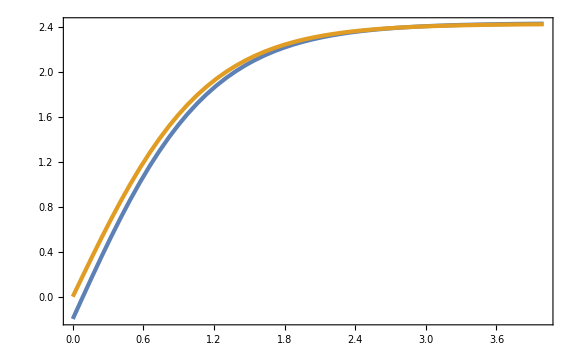

```mathematica
Plot[{βnsQCD1fit[nsm1],βnsRD1fit[nsm1]},{nsm1,0,4}]
```

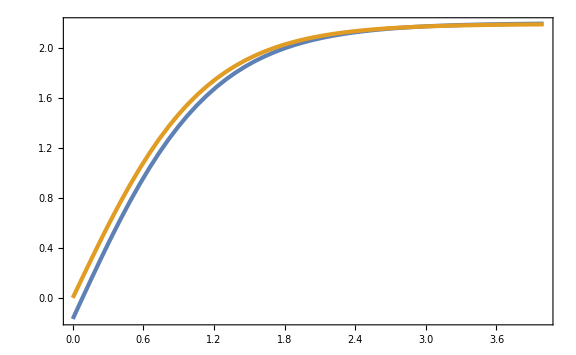

```mathematica
Plot[{βnsQCD2fit[nsm1],βnsRD2fit[nsm1]},{nsm1,0,4}]
```

```mathematica
nsm1QCD1[beta_]=1/ff ArcTanh[(beta+gg)/ee]/.{ee->2.636,ff->0.8752,gg->0.1983};
nsm1RD1[beta_]=1/ff ArcTanh[(beta+gg)/ee]/.{ee->2.431,ff->0.8975,gg->0};
nsm1QCD2[beta_]=1/ff ArcTanh[(beta+gg)/ee]/.{ee->2.370,ff->0.8648,gg->0.1686};
nsm1RD2[beta_]=1/ff ArcTanh[(beta+gg)/ee]/.{ee->2.194,ff->0.9020,gg->0};
```

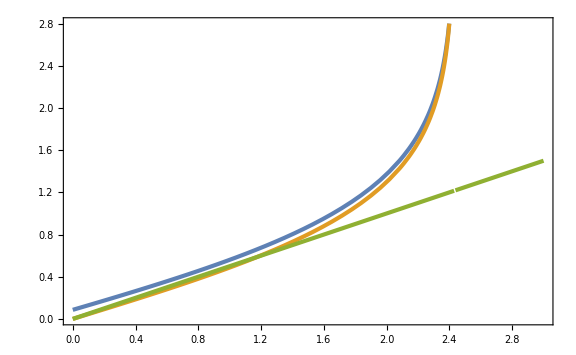

```mathematica
Plot[{nsm1QCD1[beta],nsm1RD1[beta],beta/2},{beta,0,3}]
```

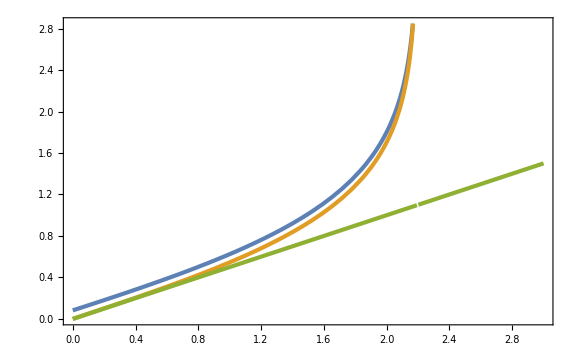

```mathematica
Plot[{nsm1QCD2[beta],nsm1RD2[beta],beta/2},{beta,0,3}]
```

```mathematica
AzQCD1[Oh2_,nsm1_]=Sqrt[Oh2/QnsQCD1fit[nsm1]];
AzRD1[Oh2_,nsm1_]=Sqrt[Oh2/QnsRD1fit[nsm1]];
AzQCD2[Oh2_,nsm1_]=Sqrt[Oh2/QnsQCD2fit[nsm1]];
AzRD2[Oh2_,nsm1_]=Sqrt[Oh2/QnsRD2fit[nsm1]];
```

```mathematica
AnsRD11s=Map[{nsm1RD1[#[[1]]],AzRD1[#[[2]],nsm1RD1[#[[1]]]]}&,Ωbeta1s];
AnsRD12s=Map[{nsm1RD1[#[[1]]],AzRD1[#[[2]],nsm1RD1[#[[1]]]]}&,Ωbeta2s];
AnsRD13s=Map[{nsm1RD1[#[[1]]],AzRD1[#[[2]],nsm1RD1[#[[1]]]]}&,Ωbeta3s];
AnsRD21s=Map[{nsm1RD2[#[[1]]],AzRD2[#[[2]],nsm1RD2[#[[1]]]]}&,Ωbeta1s];
AnsRD22s=Map[{nsm1RD2[#[[1]]],AzRD2[#[[2]],nsm1RD2[#[[1]]]]}&,Ωbeta2s];
AnsRD23s=Map[{nsm1RD2[#[[1]]],AzRD2[#[[2]],nsm1RD2[#[[1]]]]}&,Ωbeta3s];
AnsQCD11s=Map[{nsm1QCD1[#[[1]]],AzQCD1[#[[2]],nsm1QCD1[#[[1]]]]}&,Ωbeta1s];
AnsQCD12s=Map[{nsm1QCD1[#[[1]]],AzQCD1[#[[2]],nsm1QCD1[#[[1]]]]}&,Ωbeta2s];
AnsQCD13s=Map[{nsm1QCD1[#[[1]]],AzQCD1[#[[2]],nsm1QCD1[#[[1]]]]}&,Ωbeta3s];
AnsQCD21s=Map[{nsm1QCD2[#[[1]]],AzQCD2[#[[2]],nsm1QCD2[#[[1]]]]}&,Ωbeta1s];
AnsQCD22s=Map[{nsm1QCD2[#[[1]]],AzQCD2[#[[2]],nsm1QCD2[#[[1]]]]}&,Ωbeta2s];
AnsQCD23s=Map[{nsm1QCD2[#[[1]]],AzQCD2[#[[2]],nsm1QCD2[#[[1]]]]}&,Ωbeta3s];
```

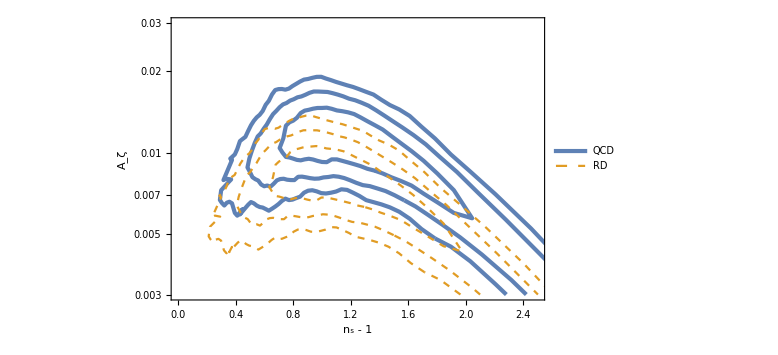

```mathematica
ListLogPlot[{AnsQCD13s,AnsQCD12s,AnsQCD11s,AnsRD13s,AnsRD12s,AnsRD11s},PlotRange->{{0,2.5},{0.003,0.03}},PlotStyle->{{Color[1],AbsoluteThickness[3]},{Color[1],AbsoluteThickness[3]},{Color[1],AbsoluteThickness[3]},{Color[2],Dashed},{Color[2],Dashed},{Color[2],Dashed}},FrameLabel->{{Subscript[A, ζ],None},{"n_(<s>) - 1","k_max = 10^8 Mpc^-1"}},PlotLegends->Placed[LineLegend[{"QCD",None,None,"RD"},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.15,0.85}]]
```

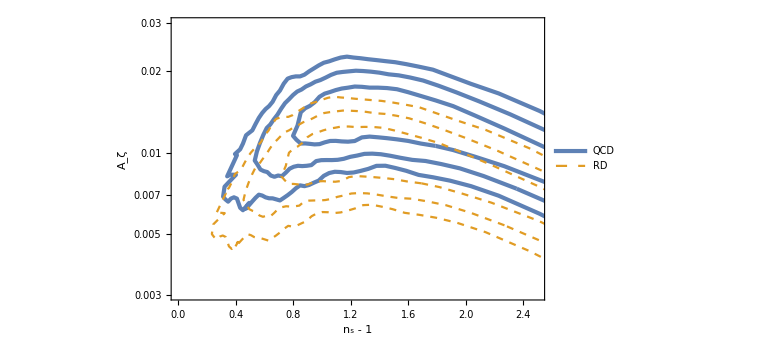

```mathematica
ListLogPlot[{AnsQCD23s,AnsQCD22s,AnsQCD21s,AnsRD23s,AnsRD22s,AnsRD21s},PlotRange->{{0,2.5},{0.003,0.03}},PlotStyle->{{Color[1],AbsoluteThickness[3]},{Color[1],AbsoluteThickness[3]},{Color[1],AbsoluteThickness[3]},{Color[2],Dashed},{Color[2],Dashed},{Color[2],Dashed}},FrameLabel->{{Subscript[A, ζ],None},{"n_(<s>) - 1","k_max = 5 × 10^7 Mpc^-1"}},PlotLegends->Placed[LineLegend[{"QCD",None,None,"RD"},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.15,0.85}]]
```

```mathematica
W[z_]=E^(-z^2/2);
```

```mathematica
16/81 Az Integrate[W[k R]^2(k R)^4(k/ks)^(ns-1)1/k,{k,0,kmax},Assumptions->{ns>0,R>0}]//Simplify
```

8/81 Az (kmax^2)^(1/2-ns/2) (kmax/(ks R))^(-1+ns) (Gamma[(3+ns)/2]-Gamma[(3+ns)/2,kmax^2 R^2])

```mathematica
δrms[R_]=Simplify[Sqrt[16/81 Az Integrate[W[k R]^2(k R)^4(k/ks)^(ns-1)1/k,{k,0,kmax},Assumptions->{ns>0,R>0}]],{kmax>0}]
```

2/9 √2 √(Az ks (1/(ks R))^ns R (Gamma[(3+ns)/2]-Gamma[(3+ns)/2,kmax^2 R^2]))

```mathematica
Msol=1.989 10^33;
```

```mathematica
1/(1.56 10^13)
```

6.41026×10^-14

```mathematica
Rsol=R/.Solve[10^20(50/106.75)^(-1/6)(R 1.56 10^13)^2==Msol,R][[2]]
```

2.68376×10^-7

```mathematica
RinM[M_]=Rsol(M/Ms)^(1/2)
```

2.68376×10^-7 √(M/Ms)

```mathematica
δrms[RinM[Ms]]
```

2/9 √2 √((3.72612×10^6)^(-1+ns) Az (kmax^2)^(1/2-ns/2) (kmax/ks)^(-1+ns) (Gamma[(3+ns)/2]-Gamma[(3+ns)/2,7.20254×10^-14 kmax^2]))

```mathematica
δrms[RinM[Ms]]/.{ns->2,Az->0.01,ks->kyr,kmax->10^8}
```

General::munfl: Exp[-710.385] is too small to represent as a normalized machine number; precision may be lost.

0.0154505

```mathematica
δrms[RinM[Ms]]/.{ns->2.2,Az->0.012,ks->kyr,kmax->5 10^7}
```

0.0148009